## General Function Board

### Ecological model - Steady states

```mathematica
dSCdt=IS-VmD SC Z/(KmD+SC)-eC SC;
dDCdt=VmD SC Z/(KmD+SC)-VmU DC M/(KmU+DC)-eD DC+dZ Z+dM M;
dMdt=γM (1-φ)VmU DC M/(KmU+DC)-dM M;
dZdt=γZ φ VmU DC M/(KmU+DC)-dZ Z;
coex=Solve[{dMdt==0,dZdt==0,dSCdt==0,dDCdt==0},{M,Z,SC,DC}]//MatrixForm
SCeq1=SC/.coex[[1,1]];
DCeq1=DC/.coex[[1,1]];
Meq1=M/.coex[[1,1]];
Zeq1=Z/.coex[[1,1]];
SCeq2=SC/.coex[[1,2]];
DCeq2=DC/.coex[[1,2]];
Meq2=M/.coex[[1,2]];
Zeq2=Z/.coex[[1,2]];
SCeq3=SC/.coex[[1,3]];
DCeq3=DC/.coex[[1,3]];
Meq3=M/.coex[[1,3]];
Zeq3=Z/.coex[[1,3]];
```

(M→0 | Z→0 | SC→IS/eC | DC→0
M→(dM IS γM+dM eD KmU γM-IS VmU γM^2-dM IS γM φ-dM eD KmU γM φ+2 IS VmU γM^2 φ-IS VmU γM^2 φ^2-(dM eC γM (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(dM eC γM φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM^2 φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(eC VmU γM^2 φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(dM^2-dM^2 γM-dM VmU γM+dM VmU γM^2+dM^2 γM φ+dM VmU γM φ-2 dM VmU γM^2 φ-dM^2 γZ φ+dM VmU γM γZ φ+dM VmU γM^2 φ^2-dM VmU γM γZ φ^2) | Z→(-dM IS γZ φ-dM eD KmU γZ φ+IS VmU γM γZ φ-IS VmU γM γZ φ^2+(dM eC γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM γZ φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(-dM dZ+dM dZ γM+dZ VmU γM-dZ VmU γM^2-dM dZ γM φ-dZ VmU γM φ+2 dZ VmU γM^2 φ+dM dZ γZ φ-dZ VmU γM γZ φ-dZ VmU γM^2 φ^2+dZ VmU γM γZ φ^2) | SC→(-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2-√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)) | DC→-(dM KmU)/(dM-VmU γM+VmU γM φ)
M→(dM IS γM+dM eD KmU γM-IS VmU γM^2-dM IS γM φ-dM eD KmU γM φ+2 IS VmU γM^2 φ-IS VmU γM^2 φ^2-(dM eC γM (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(dM eC γM φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM^2 φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(eC VmU γM^2 φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(dM^2-dM^2 γM-dM VmU γM+dM VmU γM^2+dM^2 γM φ+dM VmU γM φ-2 dM VmU γM^2 φ-dM^2 γZ φ+dM VmU γM γZ φ+dM VmU γM^2 φ^2-dM VmU γM γZ φ^2) | Z→(-dM IS γZ φ-dM eD KmU γZ φ+IS VmU γM γZ φ-IS VmU γM γZ φ^2+(dM eC γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))-(eC VmU γM γZ φ (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2))+(eC VmU γM γZ φ^2 (-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2)))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)))/(-dM dZ+dM dZ γM+dZ VmU γM-dZ VmU γM^2-dM dZ γM φ-dZ VmU γM φ+2 dZ VmU γM^2 φ+dM dZ γZ φ-dZ VmU γM γZ φ-dZ VmU γM^2 φ^2+dZ VmU γM γZ φ^2) | SC→(-dM dZ IS+dM dZ eC KmD+dM dZ IS γM-dM dZ eC KmD γM+dZ IS VmU γM-dZ eC KmD VmU γM-dZ IS VmU γM^2+dZ eC KmD VmU γM^2-dM dZ IS γM φ+dM dZ eC KmD γM φ-dZ IS VmU γM φ+dZ eC KmD VmU γM φ+2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ+dM dZ IS γZ φ-dM dZ eC KmD γZ φ+dM IS VmD γZ φ+dM eD KmU VmD γZ φ-dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ-IS VmD VmU γM γZ φ-dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2+dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2+IS VmD VmU γM γZ φ^2+√(-4 (dM dZ IS KmD-dM dZ IS KmD γM-dZ IS KmD VmU γM+dZ IS KmD VmU γM^2+dM dZ IS KmD γM φ+dZ IS KmD VmU γM φ-2 dZ IS KmD VmU γM^2 φ-dM dZ IS KmD γZ φ+dZ IS KmD VmU γM γZ φ+dZ IS KmD VmU γM^2 φ^2-dZ IS KmD VmU γM γZ φ^2) (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)+(dM dZ IS-dM dZ eC KmD-dM dZ IS γM+dM dZ eC KmD γM-dZ IS VmU γM+dZ eC KmD VmU γM+dZ IS VmU γM^2-dZ eC KmD VmU γM^2+dM dZ IS γM φ-dM dZ eC KmD γM φ+dZ IS VmU γM φ-dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ+2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ+dM dZ eC KmD γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ-dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2-dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2+dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2)^2))/(2 (-dM dZ eC+dM dZ eC γM+dZ eC VmU γM-dZ eC VmU γM^2-dM dZ eC γM φ-dZ eC VmU γM φ+2 dZ eC VmU γM^2 φ+dM dZ eC γZ φ+dM eC VmD γZ φ-dZ eC VmU γM γZ φ-eC VmD VmU γM γZ φ-dZ eC VmU γM^2 φ^2+dZ eC VmU γM γZ φ^2+eC VmD VmU γM γZ φ^2)) | DC→-(dM KmU)/(dM-VmU γM+VmU γM φ))

```mathematica
Simplify[Zeq3]
```

(γZ φ (dM dZ IS+dM dZ eC KmD+2 dM dZ eD KmU-dM dZ IS γM-dM dZ eC KmD γM-2 dM dZ eD KmU γM-dZ IS VmU γM-dZ eC KmD VmU γM+dZ IS VmU γM^2+dZ eC KmD VmU γM^2+dM dZ IS γM φ+dM dZ eC KmD γM φ+2 dM dZ eD KmU γM φ+dZ IS VmU γM φ+dZ eC KmD VmU γM φ-2 dZ IS VmU γM^2 φ-2 dZ eC KmD VmU γM^2 φ-dM dZ IS γZ φ-dM dZ eC KmD γZ φ-2 dM dZ eD KmU γZ φ-dM IS VmD γZ φ-dM eD KmU VmD γZ φ+dZ IS VmU γM γZ φ+dZ eC KmD VmU γM γZ φ+IS VmD VmU γM γZ φ+dZ IS VmU γM^2 φ^2+dZ eC KmD VmU γM^2 φ^2-dZ IS VmU γM γZ φ^2-dZ eC KmD VmU γM γZ φ^2-IS VmD VmU γM γZ φ^2+√(4 dZ eC IS KmD (dM+VmU γM (-1+φ))^2 (1+γM (-1+φ)-γZ φ) (dZ+dZ γM (-1+φ)-dZ γZ φ-VmD γZ φ)+(VmU γM (-1+φ) (-IS VmD γZ φ+dZ (IS-eC KmD) (1+γM (-1+φ)-γZ φ))+dM (-(IS+eD KmU) VmD γZ φ+dZ (IS-eC KmD) (1+γM (-1+φ)-γZ φ)))^2)))/(2 dZ (dM+VmU γM (-1+φ)) (1+γM (-1+φ)-γZ φ) (dZ+dZ γM (-1+φ)-dZ γZ φ-VmD γZ φ))

### Steady state stability - Jacobian matrix

```mathematica
J=Simplify[{{D[dSCdt,SC],D[dSCdt,DC],D[dSCdt,M],D[dSCdt,Z]},{D[dDCdt,SC],D[dDCdt,DC],D[dDCdt,M],D[dDCdt,Z]},{D[dMdt,SC],D[dMdt,DC],D[dMdt,M],D[dMdt,Z]},{D[dZdt,SC],D[dZdt,DC],D[dZdt,M],D[dZdt,Z]}}];
JA=J/.M->Meq1/.Z->Zeq1/.SC->SCeq1/.DC->DCeq1; 
JB=J/.M->Meq2/.Z->Zeq2/.SC->SCeq2/.DC->DCeq2; 
JC=J/.M->Meq3/.Z->Zeq3/.SC->SCeq3/.DC->DCeq3; 
lambdaI={{λ,0,0,0},{0,λ,0,0},{0,0,λ,0},{0,0,0,λ}};
DC=Det[JC-lambdaI];
A1C=D[D[D[DC,λ],λ],λ]/6/.λ->0;
A2C=D[D[DC,λ],λ]/2/.λ->0;
A3C=D[DC,λ]/.λ->0;
A4C=DC/.λ->0;
COND1=A1C;
COND2=A3C;
COND3=A4C;
COND4=A1C A2C A3C-A3C^2-A1C^2 A4C;
```

### Parameter sensitivity

```mathematica
SA=Abs[Log[Abs[HO]]-Log[Abs[LO]]]/Abs[Log[Abs[HP]]-Log[Abs[LP]]];
```

### Temperature dependence - Baseline scenario

```mathematica
VmDx=VmD0 Exp[-EvD/(R(x+273))];
KmDx=KmD0 Exp[-EkD/(R(x+273))];
VmUx=VmU0 Exp[-EvU/(R(x+273))];
KmUx=KmU0 Exp[-EkU/(R(x+273))];
SC3ecox=SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
DC3ecox=DCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
M3ecox=Meq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
Z3ecox=Zeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx;
φx=1-dM/(VmUx γM)-1/c;
SC3ecoevox=SC3ecox/.φ->φx;
DC3ecoevox=DC3ecox/.φ->φx;
M3ecoevox=M3ecox/.φ->φx;
Z3ecoevox=Z3ecox/.φ->φx;
```

```mathematica
φT0=φx/.x->x0;
SC3ecoφT0=SC3ecox/.φ->φT0;
SC3T0=SC3ecoevox/.x->x0/.φx->φT0;
ΔSCeco=SC3ecoφT0-SC3T0;
ΔSCecoevo=SC3ecoevox-SC3T0;
```

```mathematica
M3ecoφT0=M3ecox/.φ->φT0;
M3T0=M3ecoevox/.x->x0/.φx->φT0;
ΔMeco=M3ecoφT0-M3T0;
ΔMecoevo=M3ecoevox-M3T0;
```

```mathematica
Z3ecoφT0=Z3ecox/.φ->φT0;
Z3T0=Z3ecoevox/.x->x0/.φx->φT0;
ΔZeco=Z3ecoφT0-Z3T0;
ΔZecoevo=Z3ecoevox-Z3T0;
```

```mathematica
DC3ecoφT0=DC3ecox/.φ->φT0;
DC3T0=DC3ecoevox/.x->x0/.φx->φT0;
ΔDCeco=DC3ecoφT0-DC3T0;
ΔDCecoevo=DC3ecoevox-DC3T0;
```

```mathematica
ΔCtoteco=ΔSCeco+ΔMeco+ΔZeco+ΔDCeco;
ΔCtotecoevo=ΔSCecoevo+ΔMecoevo+ΔZecoevo+ΔDCecoevo;
```

## Q10 - Respiration*substrate (= IS)

### Q10

```mathematica
dCq10dt=IS-r0*Q10^((T-T0)/10)*Cq10;
coexq10=Solve[dCq10dt==0,Cq10];
Cq10eq=Cq10/.coexq10[[1,1]];
Respq10eq=r0*Q10^((T-T0)/10)*Cq10/.Cq10->Cq10eq
```

IS Q10^(-T/10+(T-T0)/10+T0/10)

### AWB

```mathematica
φT=φx/.x->T;
φT0=φT/.T->T0;
RespAWB=(1-γM) (1-φ)VmU DC /(KmU+DC)+(1-γZ) φ VmU DC /(KmU+DC);
RespAWBeq=RespAWB/.DC->DCeq3/.φ->φT0/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T;
```

### Plot

```mathematica
T0=10;
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
Plot[{
RespAWBeq/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Blue}}],
TicksStyle->Directive[FontSize->18]]
```

-Graphics-

```mathematica
5 10^-3*Vsol/.Vsol->0.1
```

0.0005

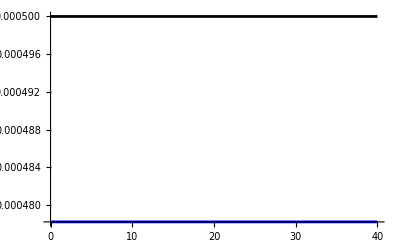

```mathematica
T0=10;
testparamq10={Q10->2,IS->5 10^-3*Vsol};
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
Plot[{Respq10eq/.testparamq10/.Vsol->0.1,
RespAWBeq/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue}}],
TicksStyle->Directive[FontSize->18]]
```

## Q10 - Respiration (rate only) - Growth only - Without Michaelis

### Q10

```mathematica
dCq10dt=IS-r0*Q10^((T-T0)/10)*Cq10;
Respq10eq=r0*Q10^((T-T0)/10)
```

Q10^((T-T0)/10) r0

### AWB

```mathematica
φT0=φx/.x->T0;
RespAWB=VmU(1-γM) (1-φ);
RespAWBeq=RespAWB/.φ->φT0/.VmU->VmUx/.x->T;
RespAWBevoeq=RespAWB/.φ->φx/.VmU->VmUx/.x->T;
```

### r0 at 10C

```mathematica
T0=10;
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
RespAWBeq/.testparamAWB/.Vsol->0.1/.T->10
RespAWBevoeq/.testparamAWB/.Vsol->0.1/.T->10
```

0.00615431

0.00615431

### Plot

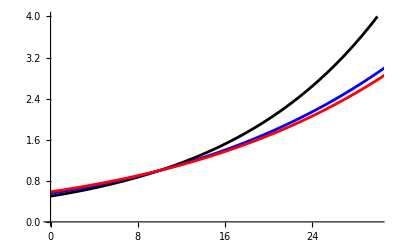

```mathematica
Plot[{Respq10eq/r0/.Q10->2,
RespAWBeq/0.00615430956058487/.testparamAWB/.Vsol->0.1,
RespAWBevoeq/0.00615430956058487/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotRange->{{0,30},{0,4}},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue,Red}}],
TicksStyle->Directive[FontSize->18]]
```

## Q10 - Respiration (rate only) - Growth only

### Q10

```mathematica
dCq10dt=IS-r0*Q10^((T-T0)/10)*Cq10;
Respq10eq=r0*Q10^((T-T0)/10)
```

Q10^((T-T0)/10) r0

### AWB

```mathematica
φT0=φx/.x->T0;
RespAWB=VmU(1-γM) (1-φ)/(KmU+DC);
RespAWBeq=RespAWB/.DC->DCeq3/.φ->φT0/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T;
RespAWBevoeq=RespAWB/.DC->DCeq3/.φ->φx/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T;
```

### r0 at 10C

```mathematica
T0=10;
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
RespAWBeq/.testparamAWB/.Vsol->0.1/.T->10
RespAWBevoeq/.testparamAWB/.Vsol->0.1/.T->10
```

0.268324

0.268324

### Plot

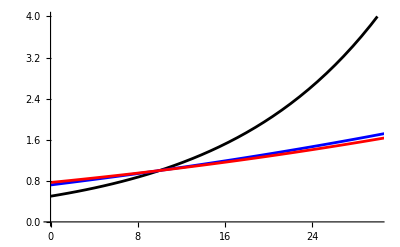

```mathematica
Plot[{Respq10eq/r0/.Q10->2,
RespAWBeq/0.2683243122085469/.testparamAWB/.Vsol->0.1,
RespAWBevoeq/0.2683243122085469/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotRange->{{0,30},{0,4}},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue,Red}}],
TicksStyle->Directive[FontSize->18]]
```

## Q10 - Respiration (rate only)

### Q10

```mathematica
dCq10dt=IS-r0*Q10^((T-T0)/10)*Cq10;
Respq10eq=r0*Q10^((T-T0)/10)
```

Q10^((T-T0)/10) r0

### AWB

```mathematica
φT0=φx/.x->T0;
RespAWB=VmU((1-γM) (1-φ) +(1-γZ) φ) /(KmU+DC);
RespAWBeq=RespAWB/.DC->DCeq3/.φ->φT0/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T;
RespAWBevoeq=RespAWB/.DC->DCeq3/.φ->φx/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T;
```

### Plot

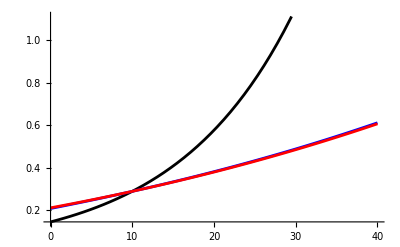

```mathematica
T0=10;
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
Plot[{Respq10eq/.Q10->2/.r0->0.28824332847003226,
RespAWBeq/.testparamAWB/.Vsol->0.1,
RespAWBevoeq/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue,Red}}],
TicksStyle->Directive[FontSize->18]]
```

### Plot normalized by r0

```mathematica
RespAWBeq/.testparamAWB/.Vsol->0.1/.T->10
RespAWBevoeq/.testparamAWB/.Vsol->0.1/.T->10
```

0.288243

0.288243

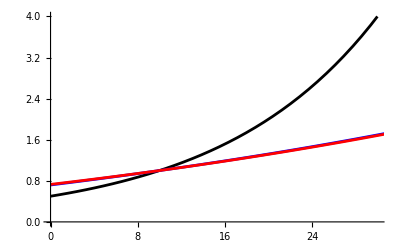

```mathematica
Plot[{Respq10eq/r0/.Q10->2,
RespAWBeq/0.2882433284700323/.testparamAWB/.Vsol->0.1,
RespAWBevoeq/0.2882433284700323/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotRange->{{0,30},{0,4}},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue,Red}}],
TicksStyle->Directive[FontSize->18]]
```

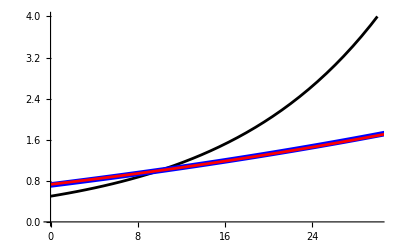

```mathematica
Plot[{Respq10eq/r0/.Q10->2,
RespAWBeq/0.2882433284700323/.testparamAWB/.Vsol->0.1,
RespAWBevoeq/0.2882433284700323/.testparamAWB/.Vsol->0.1},
{T,0,40},
PlotRange->{{0,30},{0,4}},PlotStyle->{{Black,Thickness[0.005]},{Blue,Thickness[0.01]},(*Make the blue line thicker*){Red,Thickness[0.005]}},TicksStyle->Directive[FontSize->18]]
```

## Decay rate

### Q10 model

```mathematica
decayq10=r0*Q10^((T-T0)/10);
```

```mathematica
decayq10/.Q10->2/.r0->r020/.T->20
```

0.0000851951

### AWB and AWBevo models

```mathematica
decayAWB=VmD Z/(KmD+SC)/.Z->Z3ecox/.SC->SC3ecox/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T/.φ->φT0;
decayAWBevo=VmD Z/(KmD+SC)/.Z->Z3ecox/.SC->SC3ecox/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φT/.x->T;
```

### Plot

```mathematica
T0=10;
testparamq10={Q10->2};
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
decayq10/.testparamq10/.r0->r020
decayAWBevo/.testparamAWB/.Vsol->0.1/.T->20
```

0.0000425975 2^(1/10 (-10+T))

0.0000956431

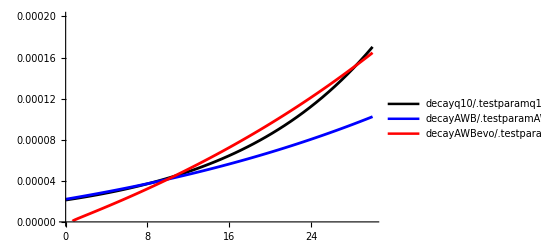

```mathematica
Plot[{decayq10/.testparamq10/.r0->r020,
decayAWB/.testparamAWB/.Vsol->0.1,
decayAWBevo/.testparamAWB/.Vsol->0.1},
{T,0,30},
PlotRange->{{0,30},{0,0.0002}},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue,Red}}],
TicksStyle->Directive[FontSize->18],
PlotLegends->"Expressions"]
```

## Q10 - soil C

### Q10 model

```mathematica
dCq10dt=IS-r0*Q10^((T-T0)/10)*Cq10;
coexq10=Solve[dCq10dt==0,Cq10]
Cq10eq=Cq10/.coexq10[[1,1]];
```

{{Cq10→(IS Q10^(1-T/10))/r0}}

### AWB and AWBevo models

```mathematica
φT=φx/.x->T;
φT0=φT/.T->T0;
SC3ecoT=SC3ecox/.x->T/.φ->φT0;
SC3ecoevoT=SC3ecox/.φ->φT/.x->T;
```

### Plot

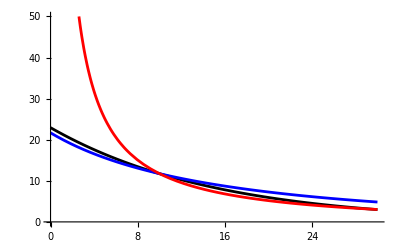

```mathematica
T0=10;
testparamq10={Q10->2,IS->5 10^-3*Vsol,eC->10^-6};
testparamAWB={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
Cq10eqAN=Cq10eq/.testparamq10/.Vsol->0.1/.T->T0
SC3ecoTAN=SC3ecoT/.testparamAWB/.Vsol->0.1/.T->T0
r020=Cq10eqAN*r0/SC3ecoTAN
Plot[{Cq10eq/.testparamq10/.Vsol->0.1/.r0->r020,
SC3ecoT/.testparamAWB/.Vsol->0.1,
SC3ecoevoT/.testparamAWB/.Vsol->0.1},
{T,0,30},
PlotRange->{{0,30},{0,50}},
PlotStyle->Table[{color,Thickness[0.005]},{color,{Black,Blue,Red}}],
TicksStyle->Directive[FontSize->18]]
```

```mathematica
Solve[Cq10eqAN==SC3ecoTAN,r0]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{r0→0.0000415975}}

### Plot legend

```mathematica
Plot[{Cq10eq/.testparamq10/.Vsol->0.1/.r0->r020,SC3ecoT/.testparamAWB/.Vsol->0.1,SC3ecoevoT/.testparamAWB/.Vsol->0.1},{T,0,30},PlotRange->{{0,30},{0,50}},PlotStyle->{Black,Blue,Red},AxesLabel->{"Temperature (°C)","Soil C steady state (g.m-2)"},LabelStyle->{FontSize->14},TicksStyle->Directive[FontSize->14],PlotLegends->Placed[{"Q10","AWB","AWBevo"},{0.7,0.6}]]
```

## Figure C as a function of phi

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
SC3ecoxVsol = SC3ecox/.testparam/.Vsol->0.1;
SC3ecoxVsol/.x->5/.φ->0.1
```

11.4475

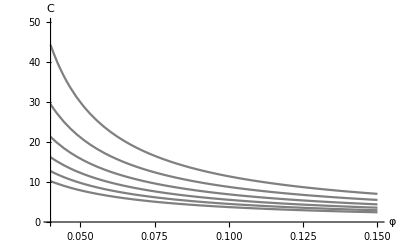

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
SC3ecoxVsol = SC3ecox/.testparam/.Vsol->0.1;
Plot[{SC3ecoxVsol/.x->5, SC3ecoxVsol/.x->10,SC3ecoxVsol/.x->15,SC3ecoxVsol/.x->20,SC3ecoxVsol/.x->25,,SC3ecoxVsol/.x->30},{φ,0.04,0.15},PlotRange->{{0.04,0.15},{0,50}},
PlotStyle->{Gray},AxesLabel->{"φ","C"}]
```

## Figure of phi=f(T)

```mathematica
φx
```

1-1/c-(dM ⅇ^(EvU/(R (273+x))))/(VmU0 γM)

```mathematica
φx/.testparam/.x->30
```

0.122349

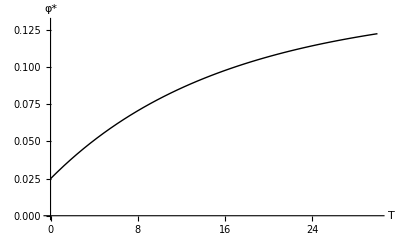

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
Plot[φx/.testparam,{x,0,30},AxesOrigin->{0,0},PlotRange->{{0,30},{0,0.13}},
PlotStyle->{Black,Thick},AspectRatio->0.6,AxesLabel->{"T","φ*"},AxesLabel->None]
```

#### When dM sensitive to T

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=Simplify[φx/.x->xref+dx/.dM->dMx]
```

1-1/c-(dMref ⅇ^((EvU/(273+dx+xref)+EadM (-1/(273+x)+1/(273+xref)))/R))/(VmU0 γM)

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
Plot[φdMx/.testparam,{x,0,30},AxesOrigin->{0,0},PlotRange->{{0,30},{0,0.13}},
PlotStyle->{Black,Thick},AspectRatio->0.6,AxesLabel->{"T","φ*"},AxesLabel->None]
```

## Figure w Absiko, Amazon, Marseilles

```mathematica
SC3adaptT0*100
```

3090.56

```mathematica
(SC3ecodMx/.dx->5)*100
```

2166.21

```mathematica
(SC3ecoevodMx/.dx->5)*100
```

1304.28

```mathematica
3090.558874838588-1304.2807500665012
```

1786.28

122.815

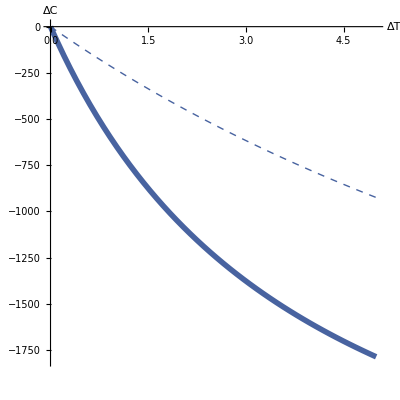

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->4.1,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-1800,0}},
PlotStyle->{{RGBColor["#4863A0"],Dashed,Thick},{RGBColor["#4863A0"],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}]
```

122.815

66.5525

26.6872

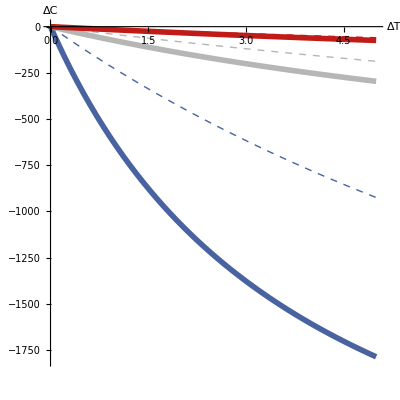

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->4.1,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-1800,0}},
PlotStyle->{{RGBColor["#4863A0"],Dashed,Thick},{RGBColor["#4863A0"],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->12.6,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],Dashed,Thick},{RGBColor["#B6B6B4"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->26.9,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],Dashed,Thick},{RGBColor["#C11B17"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

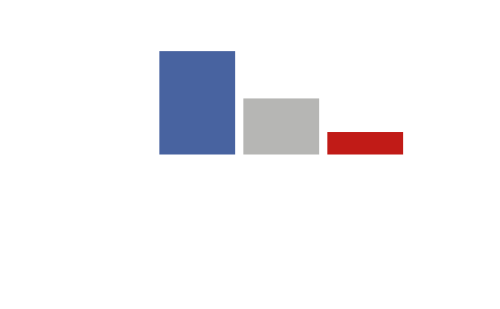

```mathematica
BarChart[{{122.8,66.6,26.7}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{{RGBColor["#4863A0"],RGBColor["#B6B6B4"],RGBColor["#C11B17"]}},
ImageSize->500,AxesLabel->None, Axes->None,ChartBaseStyle->EdgeForm[None]]
```

122.815

66.5525

26.6872

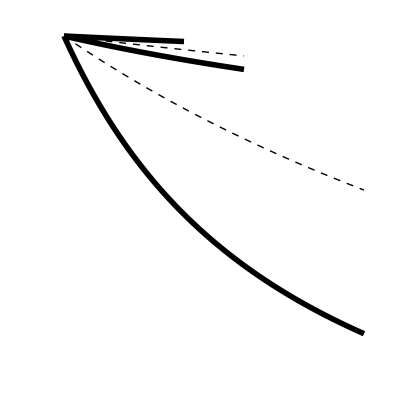

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->4.1,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},Axes->None,PlotRange->{{0,5},{-1800,0}},
PlotStyle->{{Black,Dashed,Thick},{Black,Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->12.6,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,3},PlotStyle->{{Black,Dashed,Thick},{Black,Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*Vsol,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*Vsol,EkU->21,KmD0->3.3 10^4*Vsol,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->26.9,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam/.Vsol->0.1;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam/.Vsol->0.1;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam/.Vsol->0.1;
ΔSCecodM=(SC3ecodMx-SC3adaptT0)*100;
ΔSCecoevodM=(SC3ecoevodMx-SC3adaptT0)*100;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,2},PlotStyle->{{Black,Dashed,Thick},{Black,Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

## With constitutive enzyme production

### Ecological model - Steady states

```mathematica
dSCdt=IS-VmD SC Z/(KmD+SC)-eC SC;
dDCdt=VmD SC Z/(KmD+SC)-VmU DC M/(KmU+DC)-eD DC+dZ Z+dM M;
dMdt=γM (1-φ)VmU DC M/(KmU+DC)-dM M-rZ M;
dZdt=γZ φ VmU DC M/(KmU+DC)-dZ Z+rZ M;
coex=Solve[{dMdt==0,dZdt==0,dSCdt==0,dDCdt==0},{M,Z,SC,DC}]//MatrixForm
SCeq1=SC/.coex[[1,1]];
DCeq1=DC/.coex[[1,1]];
Meq1=M/.coex[[1,1]];
Zeq1=Z/.coex[[1,1]];
SCeq2=SC/.coex[[1,2]];
DCeq2=DC/.coex[[1,2]];
Meq2=M/.coex[[1,2]];
Zeq2=Z/.coex[[1,2]];
SCeq3=SC/.coex[[1,3]];
DCeq3=DC/.coex[[1,3]];
Meq3=M/.coex[[1,3]];
Zeq3=Z/.coex[[1,3]];
```

(1)
 |  |  |  |

```mathematica
dMmutdt=γM (1-φmut)VmU DC(1+u[φmut-φres]) Mmut/(KmU+DC(1+u[φmut-φres]))-dM Mmut-rZ Mmut/.DC->DCeq3/.φ->φres;
```

```mathematica
fitness=Simplify[dMmutdt/Mmut]
```

-((dM+rZ) (VmU γM (φmut-φres)+(dM+rZ+VmU γM (-1+φmut)) u[φmut-φres]))/(-VmU γM (-1+φres)+(dM+rZ) u[φmut-φres])

```mathematica
gradient1=Simplify[D[fitness,φmut]]
```

((dM+rZ) ((dM+rZ) (VmU γM (φmut-φres)+(dM+rZ+VmU γM (-1+φmut)) u[φmut-φres]) u'[φmut-φres]-(-VmU γM (-1+φres)+(dM+rZ) u[φmut-φres]) (VmU γM+VmU γM u[φmut-φres]+(dM+rZ+VmU γM (-1+φmut)) u'[φmut-φres])))/(VmU γM (-1+φres)-(dM+rZ) u[φmut-φres])^2

```mathematica
gradient2=Simplify[gradient1/.φmut->φres]
```

((dM+rZ) ((dM+rZ) (dM+rZ+VmU γM (-1+φres)) u[0] u'[0]-(VmU (γM-γM φres)+(dM+rZ) u[0]) (VmU γM+VmU γM u[0]+(dM+rZ+VmU γM (-1+φres)) u'[0])))/(VmU γM (-1+φres)-(dM+rZ) u[0])^2

```mathematica
gradient3=Simplify[gradient2/.u[0]->0/.φres->φ]
```

((dM+rZ) ((dM+rZ) u'[0]+VmU (γM+γM (-1+φ) u'[0])))/(VmU γM (-1+φ))

```mathematica
φstab=Simplify[Solve[gradient3==0,φ][[1,1,2]]]
```

1-dM/(VmU γM)-rZ/(VmU γM)-1/u'[0]

## Global projections

#### Checking global results

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*0.1,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*0.1,EkU->21,KmD0->3.3 10^4*0.1,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
```

```mathematica
M3ecox+SC3ecox/.φ->φdMT0/.dM->dMx/.γM->0.3/.x->4.49/.testparam
```

29.8724

#### phi = f(T) (Fig 3a)

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*0.1,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*0.1,EkU->21,KmD0->3.3 10^4*0.1,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
```

```mathematica
SC3ecoevox+M3ecoevox/.testparam/.x->3.5
```

37.5109

```mathematica
SC3ecox+M3ecox/.φ->φT0/.testparam/.x0->3.5/.x->4.9
```

33.469

```mathematica
SC3ecoevox+M3ecoevox/.testparam/.x->4.9
```

26.5341

eAWB loss = Ceco (4.9) - Cecoevo (3.5) = - 4.05

opt-eAWB loss = Cecoevo (4.9) - Cecoevo (3.5) = - 10.98

```mathematica
26.534088739554623-33.469021746424936
```

-6.93493

#### Plot 1 = soil C eco - ecoevo

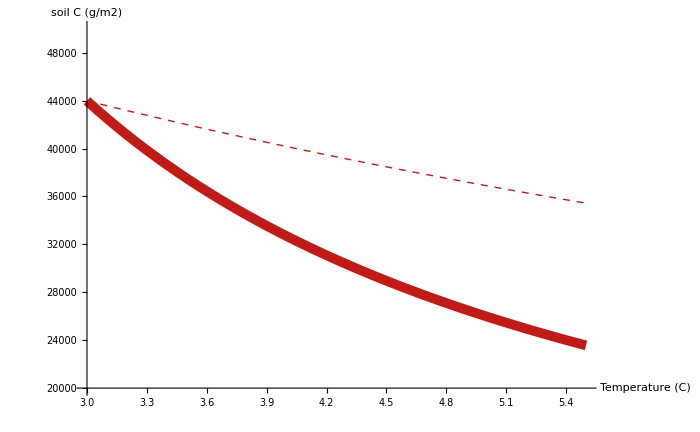

```mathematica
Plot[{(SC3ecox+M3ecox/.φ->φT0/.x0->3/.testparam)*1000,(SC3ecoevox+M3ecoevox/.testparam)*1000},{x,3,5.5},
PlotRange->{{3,5.5},{20000,50000}},
PlotStyle->{{RGBColor["#C11B17"],Dashed,Thick},{RGBColor["#C11B17"],Thickness[0.01]}},
LabelStyle->Directive[FontSize->20],
ImageSize->700,
AxesLabel->{"Temperature (C)","soil C (g/m2)"}]
```

#### Plot 3 = soilC, SOC, Meco

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*0.1,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*0.1,EkU->21,KmD0->3.3 10^4*0.1,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
```

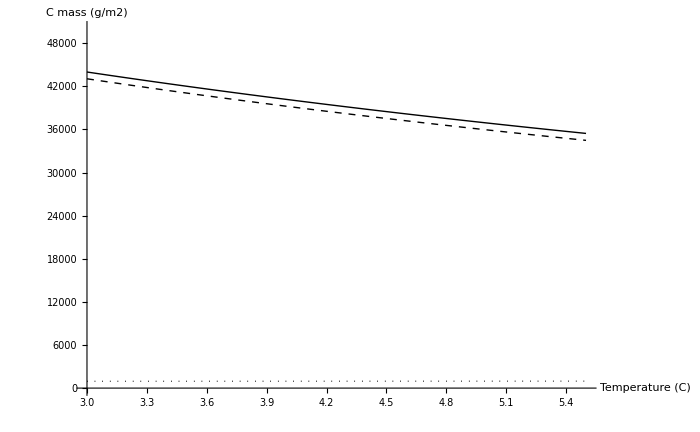

```mathematica
Plot[{(SC3ecox+M3ecox/.φ->φT0/.x0->3/.testparam)*1000,(SC3ecox/.φ->φT0/.x0->3/.testparam)*1000,(M3ecox/.φ->φT0/.x0->3/.testparam)*1000},{x,3,5.5},
PlotRange->{{3,5.5},{0,50000}},
PlotStyle->{{Black,Thick},{Black,Dashed,Thick},{Black,Dotted,Thick}},
LabelStyle->Directive[FontSize->20],
ImageSize->700,
AxesLabel->{"Temperature (C)","C mass (g/m2)"}]
```

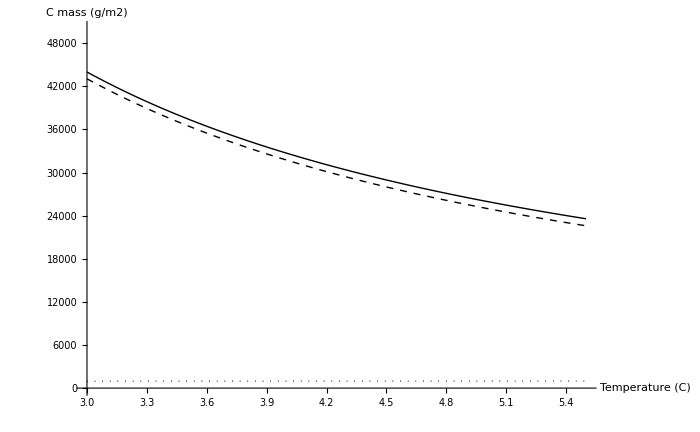

```mathematica
Plot[{(SC3ecoevox+M3ecoevox/.x0->3/.testparam)*1000,(SC3ecoevox/.x0->3/.testparam)*1000,(M3ecoevox/.x0->3/.testparam)*1000},{x,3,5.5},
PlotRange->{{3,5.5},{0,50000}},
PlotStyle->{{Black,Thick},{Black,Dashed,Thick},{Black,Dotted,Thick}},
LabelStyle->Directive[FontSize->20],
ImageSize->700,
AxesLabel->{"Temperature (C)","C mass (g/m2)"}]
```

#### Plot 4 = VmaxU,KmU,phi(T)

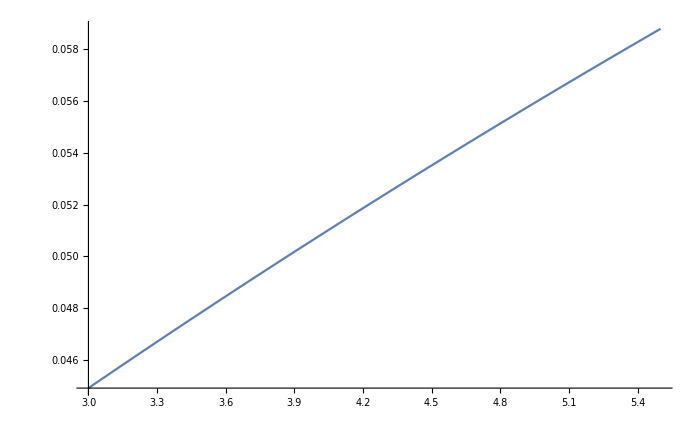

```mathematica
Plot[{φx/.testparam},{x,3,5.5},
LabelStyle->Directive[FontSize->20],
ImageSize->700]
```

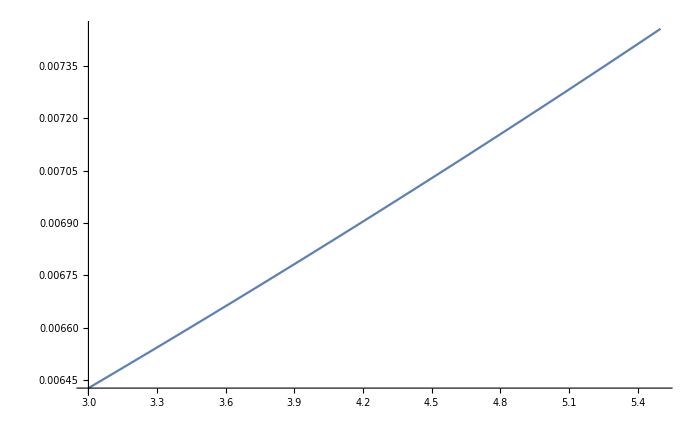

```mathematica
Plot[{VmUx/.testparam},{x,3,5.5},
LabelStyle->Directive[FontSize->20],
ImageSize->700]
```

```mathematica
Plot[{φx/.testparam},{x,3,5.5},
LabelStyle->Directive[FontSize->20],
ImageSize->700]
```

#### Plot 4 = VmaxU,KmU,phi(T) with variable x

```mathematica
TwoAxisPlot[{f_,g_},{x_,x1_,x2_}]:=Module[{fgraph,ggraph,frange,grange,fticks,gticks},{fgraph,ggraph}=MapIndexed[Plot[#,{x,x1,x2},Axes->True,PlotStyle->ColorData[1][#2[[1]]]]&,{f,g}];{frange,grange}=(PlotRange/.AbsoluteOptions[#,PlotRange])[[2]]&/@{fgraph,ggraph};fticks=N@FindDivisions[frange,5];
gticks=Quiet@Transpose@{fticks,ToString[NumberForm[#,2],StandardForm]&/@Rescale[fticks,frange,grange]};
Show[fgraph,ggraph/.Graphics[graph_,s___]:>Graphics[GeometricTransformation[graph,RescalingTransform[{{0,1},grange},{{0,1},frange}]],s],Axes->False,Frame->True,FrameStyle->{ColorData[1]/@{1,2},{Automatic,Automatic}},FrameTicks->{{fticks,gticks},{Automatic,Automatic}}]]
```

```mathematica
VmUx[x_]=VmU0 Exp[-EvU/(R(x+273))];
φx[x_]=1-dM/(VmUx[x] γM)-1/c;
φT0=φx[x]/.x->x0;
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*0.1,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*0.1,EkU->21,KmD0->3.3 10^4*0.1,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
```

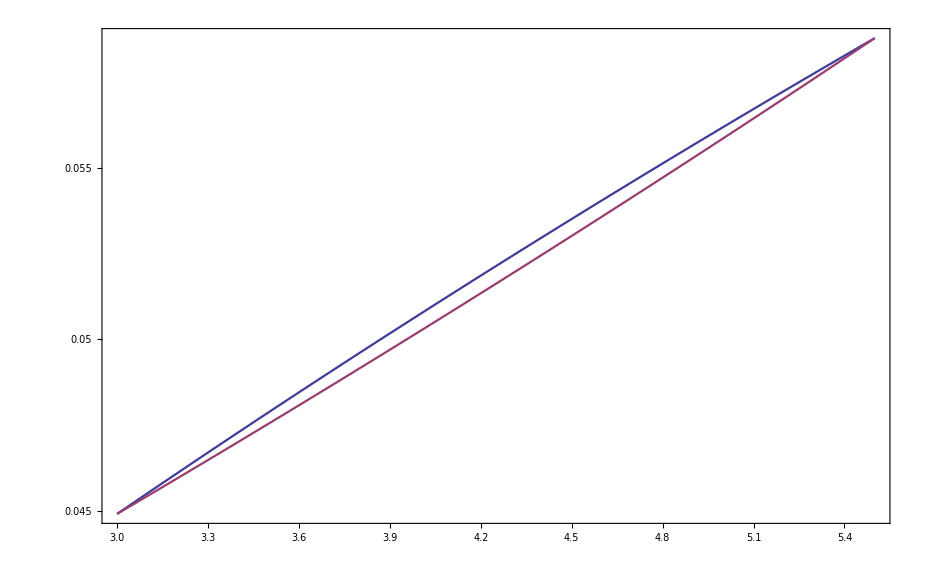

```mathematica
TwoAxisPlot[{φx[x]/.testparam,VmUx[x]/.testparam},{x,3,5.5}]
```

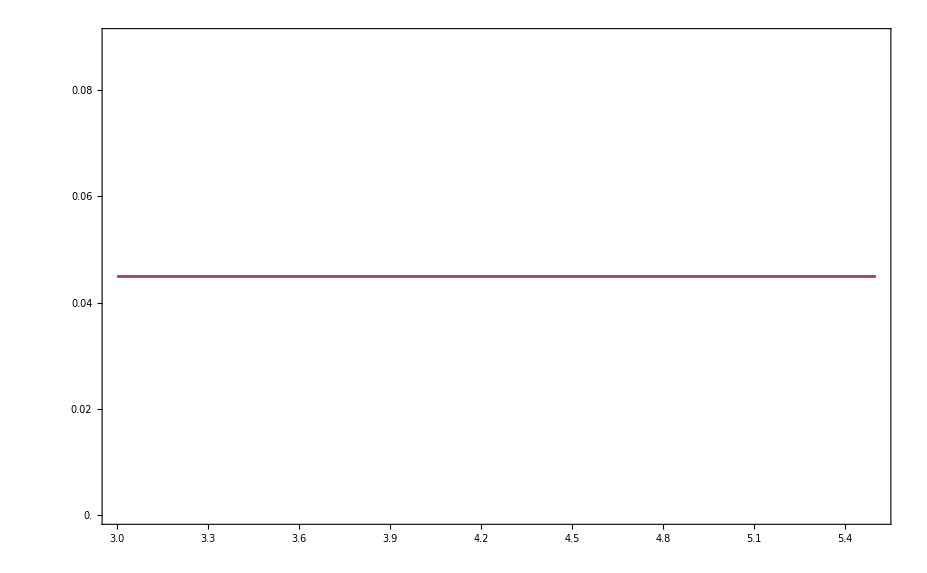

```mathematica
TwoAxisPlot[{φx[x]/.x->x0/.x0->3/.testparam,VmUx[x]/.x->x0/.x0->3/.testparam},{x,3,5.5}]
```

#### Plot 5 = C vs phi

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3*0.1,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3*0.1,EkU->21,KmD0->3.3 10^4*0.1,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17};
```

```mathematica
φx/.testparam/.x->3
```

0.0449176

```mathematica
φx/.testparam/.x->5
```

0.0561919

```mathematica
SC3ecox/.testparam/.x->3/.φ->0.044917607617602634
```

43.0427

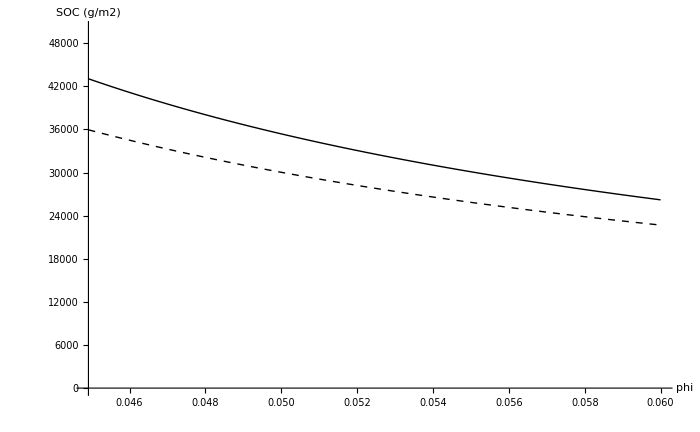

```mathematica
Plot[{(SC3ecox/.testparam/.x->3)*1000,(SC3ecox/.testparam/.x->5)*1000},{φ,0.044917607617602634,0.06},
PlotRange->{{0.044917607617602634,0.06},{0,50000}},
PlotStyle->{{Black,Thick},{Black,Dashed,Thick}},
LabelStyle->Directive[FontSize->20],
ImageSize->700,
AxesLabel->{"phi","SOC (g/m2)"}]
```

#### Derivative of phi*

```mathematica
VmUx=VmU0 Exp[-EvU/(R(x+273))];
φx=1-dM/(VmUx γM)-1/c;
```

```mathematica
φx
```

1-1/c-(dM ⅇ^(EvU/(R (273+x))))/(VmU0 γM)

```mathematica
D[φx,x]
```

(dM ⅇ^(EvU/(R (273+x))) EvU)/(R VmU0 (273+x)^2 γM)

```mathematica
fx=1-1/Exp[-1/x];
```

```mathematica
D[fx,x]
```

ⅇ^(1/x)/x^2

```mathematica
Simplify[D[D[fx,x],x]]
```

-(ⅇ^(1/x) (1+2 x))/x^4

## Work on Figure 1b - 2.0

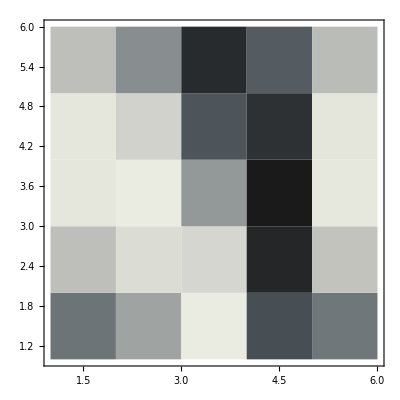
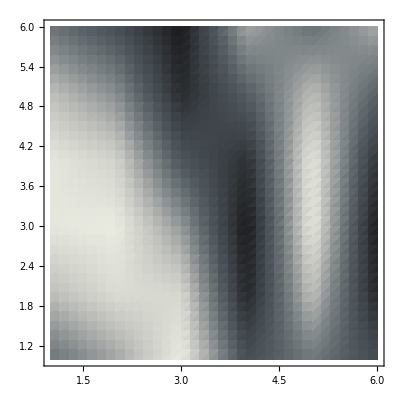
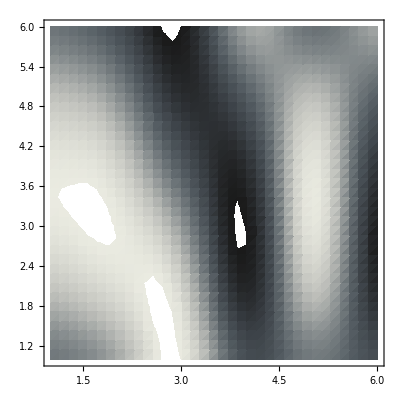
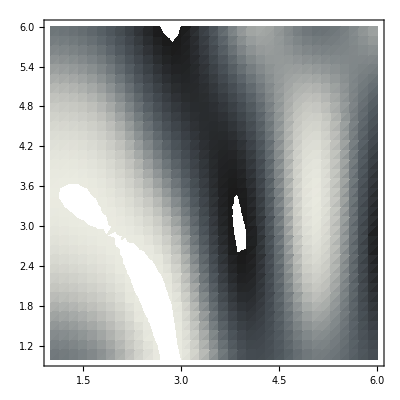

```mathematica
data=Table[Sin[j^2+i],{i,0,Pi,Pi/5},{j,0,Pi,Pi/5}];
Table[ListDensityPlot[data,Mesh->None,InterpolationOrder->o,ColorFunction->"GrayTones"],{o,{0,1,2,3}}]
```

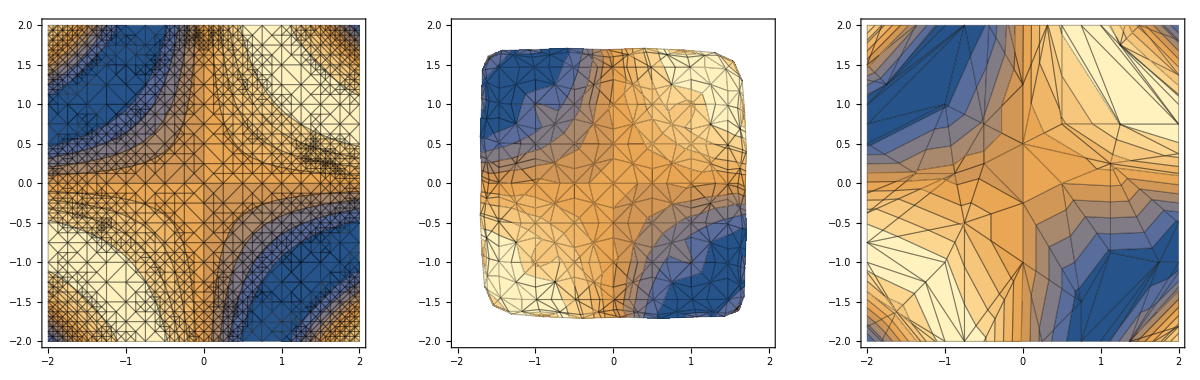

```mathematica
GraphicsRow[ContourPlot[Sin[x y],{x,-2,2},{y,-2,2},Mesh->All,PlotPoints->5,Method->{#}]&/@{Automatic,"Subdivision"->"Loop","PolygonReduction"->100}]
```

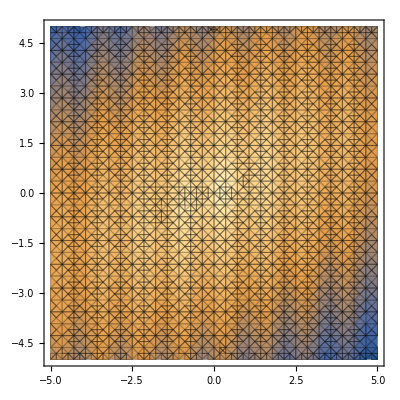

```mathematica
a[x_]:=Sin[5 x]
b[x_,y_]:=Sqrt[2 x^2+3 y^2-2 x y]
DensityPlot[a[x]-b[x,y],{x,-5,5},{y,-5,5},Mesh->All]
```

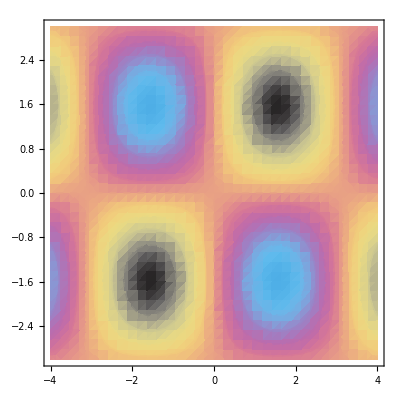

```mathematica
DensityPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3},ColorFunction->"CMYKColors",PlotPoints->35,MeshFunctions->{#3&,#3&},Mesh->{Range[-1,1,0.4],Range[-0.8,0.8,0.4]},MeshStyle->{Black,Dashed}]
```

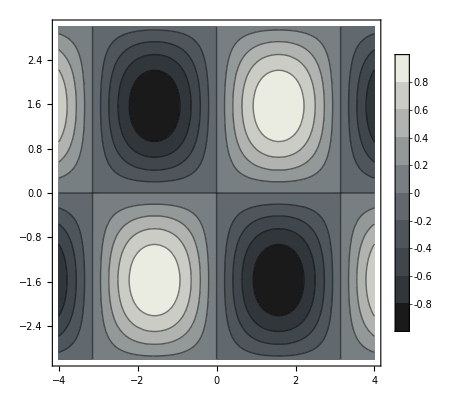

```mathematica
ContourPlot[Sin[x] Sin[y],{x,-4,4},{y,-3,3},ColorFunction->"GrayTones",PlotLegends->Automatic]
```

#### DensityPlot - not log

```mathematica
DensityPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},AxesLabel->{"φ","T"},
RegionFunction->Function[{φ,x,z}],
PlotRange->Full,ColorFunctionScaling->False,FrameTicks->None,ColorFunction->(ColorData["GrayTones"][LogarithmicScaling[#,600,10]]&),
PlotLegends->LogScaleLegend[600,10,ColorData["GrayTones"],350,LegendLabel->"C"]]
```

#### DensityPlot - log

DensityPlot::invregion: ({φ,x,z}&)[Identity[#1],Identity[#2],Identity[#3]]& must be a Boolean function.

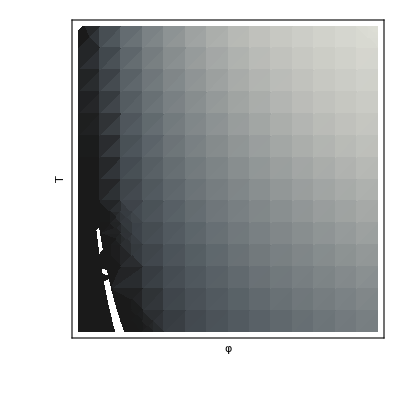

```mathematica
DensityPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},AxesLabel->{"φ","T"},
RegionFunction->Function[{φ,x,z}],
PlotRange->Full,ColorFunctionScaling->False,FrameTicks->None,ColorFunction->(ColorData["GrayTones"][LogarithmicScaling[#,600,10]]&),
PlotLegends->LogScaleLegend[600,10,ColorData["GrayTones"],350,LegendLabel->"C"]]
```

#### Separate data and contourplot

```mathematica
data=Table[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40}];
ListContourPlot[data,ContourLabels->Automatic,Contours->20,ColorFunction->"GrayTones",ClippingStyle->Automatic,PlotLegends->Automatic]
```

ListContourPlot::gmat: {{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.},{5000.}} is not a rectangular array larger than 2 x 2.

ListContourPlot[{{5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.,5000.}},ContourLabels→Automatic,Contours→20,ColorFunction→GrayTones,ClippingStyle→Automatic,PlotLegends→Automatic]

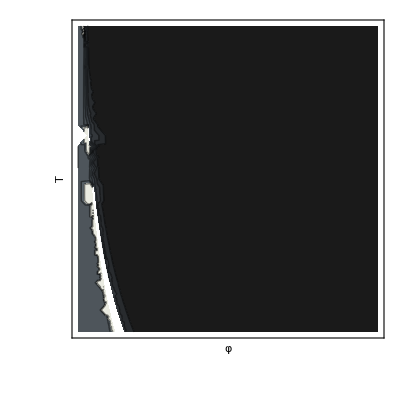

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
AxesLabel->{"φ","T"},
PlotRange->Full,
ColorFunctionScaling->True,
FrameTicks->None,
ColorFunction->"GrayTones",
PlotLegends->LogScaleLegend[600,10,ColorData["GrayTones"],350,LegendLabel->"C"]]
```

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
AxesLabel->{"φ","T"},
RegionFunction->Function[{φ,x,z}],
PlotRange->Full,
ColorFunctionScaling->False,
FrameTicks->None,
ColorFunction->(ColorData["GrayTones"][LogarithmicScaling[#,600,10]]&),
PlotLegends->LogScaleLegend[600,10,ColorData["GrayTones"],350,LegendLabel->"C"]]
```

#### Normal + Log - stack example

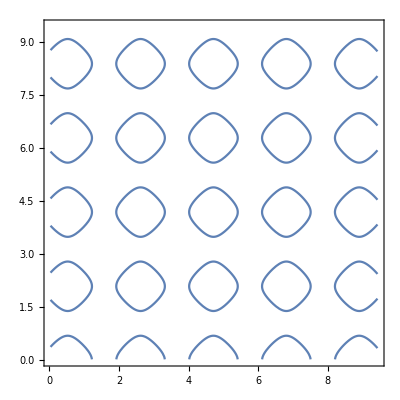

```mathematica
pl=Normal@ContourPlot[Sin[3 x]+Cos[3 y]==1/2,{x,.01 Pi,3 Pi},{y,.01 Pi,3 Pi},PlotPoints->30]
```

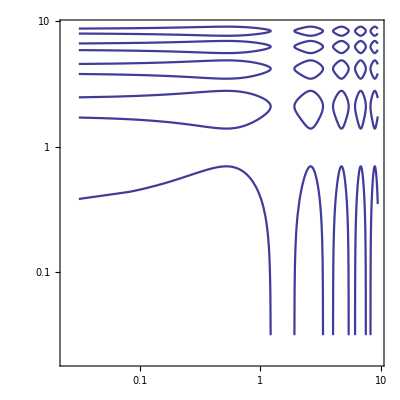

```mathematica
ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]
```

#### Normal + Log - without Normal@

```mathematica
pl=ContourPlot[Sin[3 x]+Cos[3 y]==1/2,{x,.01 Pi,3 Pi},{y,.01 Pi,3 Pi},PlotPoints->30]
```

-Graphics-

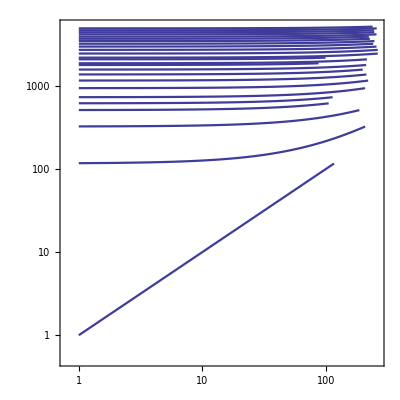

```mathematica
ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]
```

#### Normal + Log - My data

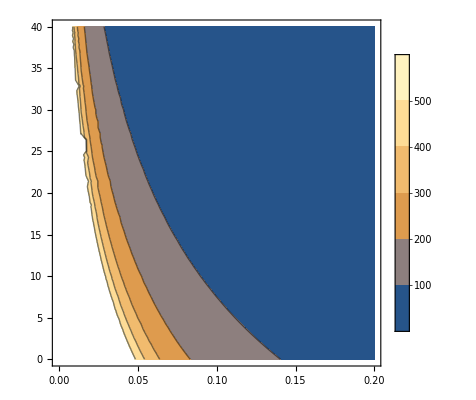

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},PlotLegends->Automatic]
```

```mathematica
pl=Normal@ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},PlotLegends->Automatic]
```

-Graphics-

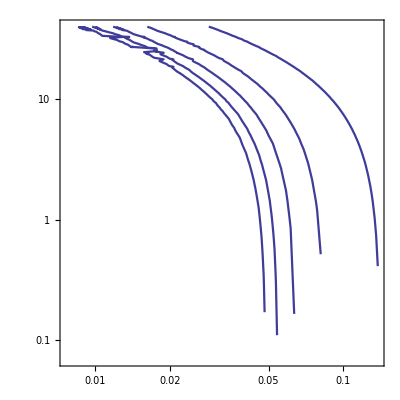

```mathematica
ListLogLogPlot[Cases[pl,Line[a_,b___]:>a,Infinity],Joined->True,Frame->True,PlotRange->All,AspectRatio->1,PlotStyle->ColorData[1][1]]
```

#### ContourPlot + Reverse GrayTones

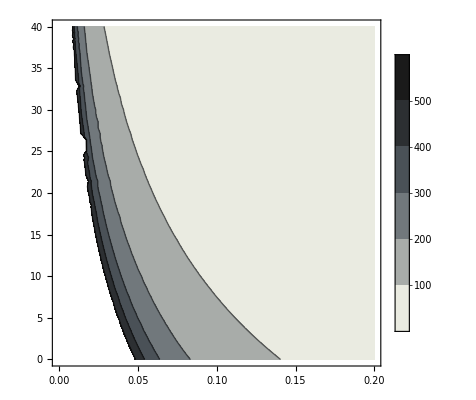

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
ColorFunction->(ColorData["GrayTones",(1-#)]&),PlotLegends->Automatic]
```

#### ContourPlot + Reverse GrayTones + ColorFunctionScaling = True -- NO CHANGE --

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
ColorFunctionScaling->True,
ColorFunction->(ColorData["GrayTones",(1-#)]&),PlotLegends->Automatic]
```

-Graphics-

#### ContourPlot + Reverse GrayTones + PlotRange = Full

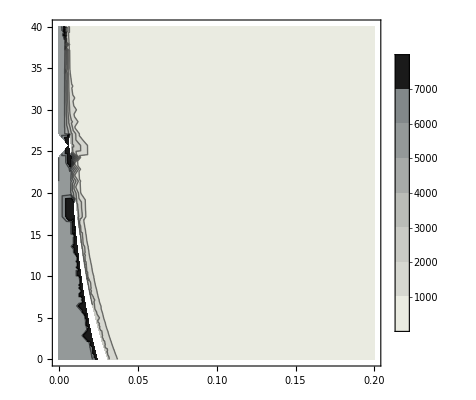

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
PlotRange->Full,
ColorFunction->(ColorData["GrayTones",(1-#)]&),PlotLegends->Automatic]
```

#### ContourPlot + Reverse GrayTones + PlotRange = specific

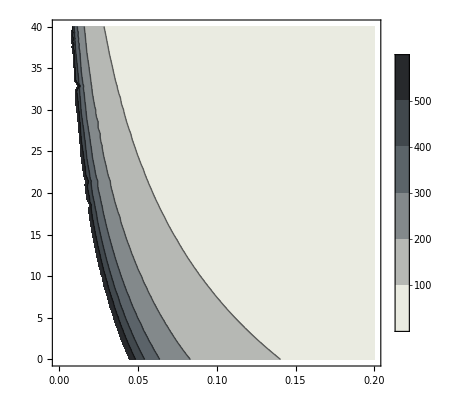

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
PlotRange->{{0,0.2},{0,40},{10,600}},
ColorFunction->(ColorData["GrayTones",(1-#)]&),PlotLegends->Automatic]
```

#### Package + Log scale

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
AxesLabel->{"φ","T"},
PlotRange->{{0,0.2},{0,40},{10,600}},
ColorFunction->(ColorData["GrayTones"][LogarithmicScaling[#,10,600]]&),
PlotLegends->Automatic]
```

-Graphics-

#### Package #1 + ScalingFunctions = Package #2

#### Package #2 + Contours = 20

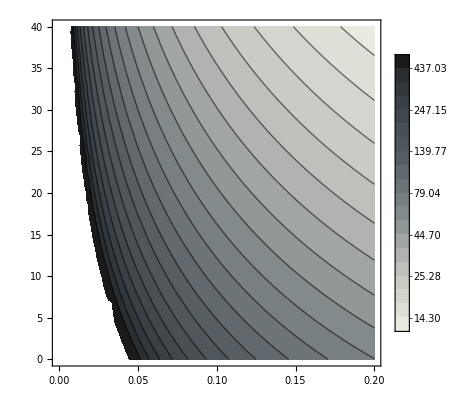

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
PlotLegends->Automatic]
```

#### Package #2 + Contours=20 + ContourStyle=None = Package #3

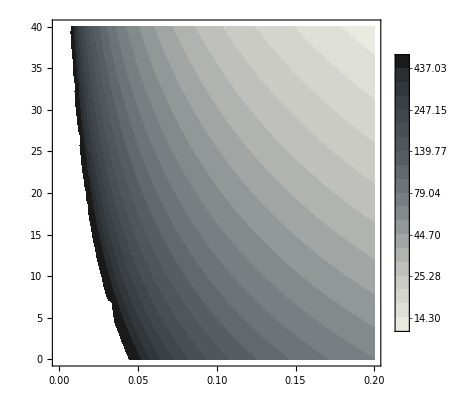

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
ContourStyle->None,
PlotLegends->Automatic]
```

## Figure 1b - 2.0 - finale

### Figure 1 carre baseline

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
COND1xφ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND2xφ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND3xφ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND4xφ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
M3ecoxφ=M3ecox/.dM->dMx/.testparam;
```

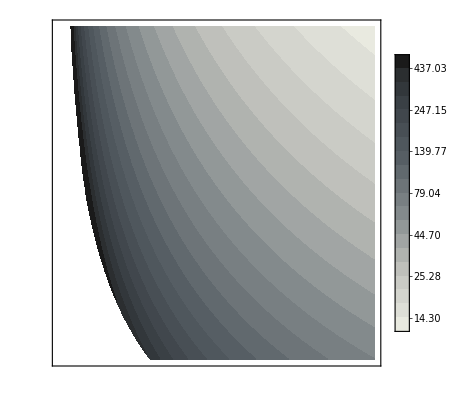

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
RegionFunction->Function[{φ,x,z},Evaluate[Im[M3ecoxφ]==0&&M3ecoxφ>0&&COND1xφ>0&&COND2xφ>0&&COND3xφ>0&&COND4xφ>0]],
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
ContourStyle->None,
FrameTicks->None,
PlotLegends->Automatic]
```

### Figure 1 carre dM=25

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->25};
COND1xφ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND2xφ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND3xφ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND4xφ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
M3ecoxφ=M3ecox/.dM->dMx/.testparam;
```

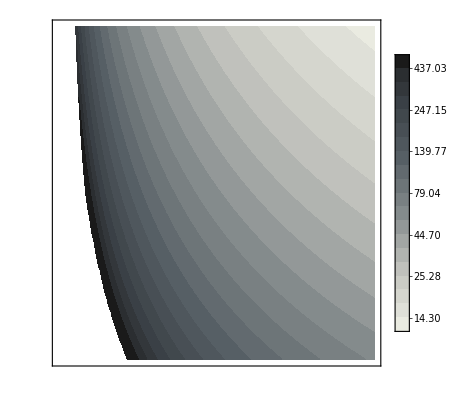

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
RegionFunction->Function[{φ,x,z},Evaluate[Im[M3ecoxφ]==0&&M3ecoxφ>0&&COND1xφ>0&&COND2xφ>0&&COND3xφ>0&&COND4xφ>0]],
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
ContourStyle->None,
FrameTicks->None,
PlotLegends->Automatic]
```

### Figure 1 carre dM=55

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->55};
COND1xφ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND2xφ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND3xφ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND4xφ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
M3ecoxφ=M3ecox/.dM->dMx/.testparam;
```

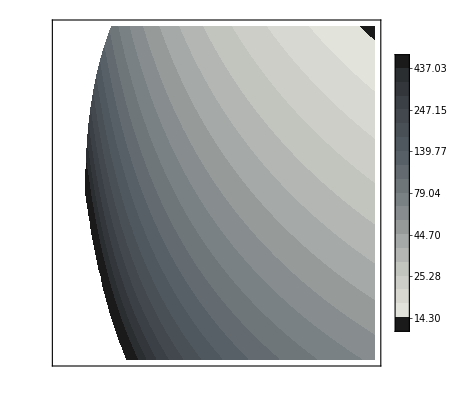

```mathematica
ContourPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},
RegionFunction->Function[{φ,x,z},Evaluate[Im[M3ecoxφ]==0&&M3ecoxφ>0&&COND1xφ>0&&COND2xφ>0&&COND3xφ>0&&COND4xφ>0]],
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
ContourStyle->None,
FrameTicks->None,
PlotLegends->Automatic]
```

### lower MGE

```mathematica
γMx=γMref+m(x-xref);
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,m->-0.014};
COND1xφ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.γM->γMx/.testparam;
COND2xφ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.γM->γMx/.testparam;
COND3xφ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.γM->γMx/.testparam;
COND4xφ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.γM->γMx/.testparam;
M3ecoxφ=M3ecox/.γM->γMx/.testparam;
```

```mathematica
SC3ecox/.γM->γMx/.testparam/.φ->0.2/.x->30
```

21.5465

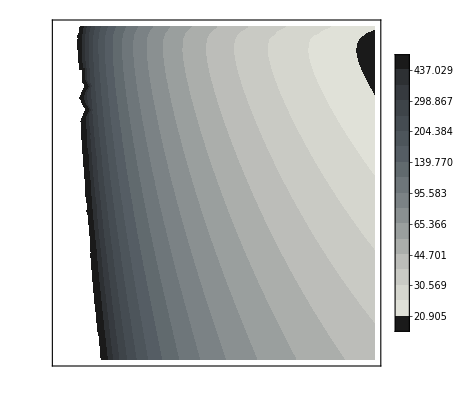

```mathematica
ContourPlot[SC3ecox/.γM->γMx/.testparam,{φ,0,0.2},{x,0,40},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
ContourStyle->None,
FrameTicks->None,
PlotLegends->Automatic]
```

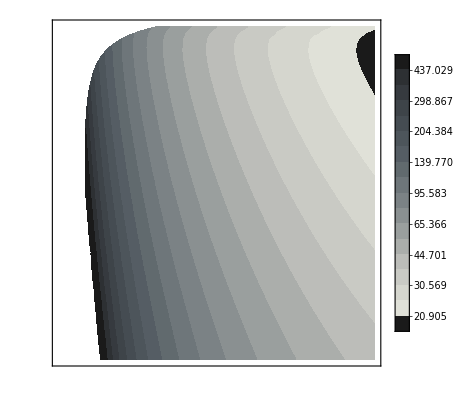

```mathematica
ContourPlot[SC3ecox/.γM->γMx/.testparam,{φ,0,0.2},{x,0,40},
RegionFunction->Function[{φ,x,z},Evaluate[Im[M3ecoxφ]==0&&M3ecoxφ>0&&COND1xφ>0&&COND2xφ>0&&COND3xφ>0&&COND4xφ>0]],
ColorFunction->(ColorData["GrayTones",(1-#)]&),
ScalingFunctions->{None,None,"Log"},
PlotRange->{{0,0.2},{0,40},{10,600}},
Contours->20,
ContourStyle->None,
FrameTicks->None,
PlotLegends->Automatic]
```

## Figure 1b

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
COND1xφ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND2xφ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND3xφ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
COND4xφ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.testparam;
M3ecoxφ=M3ecox/.dM->dMx/.testparam;
```

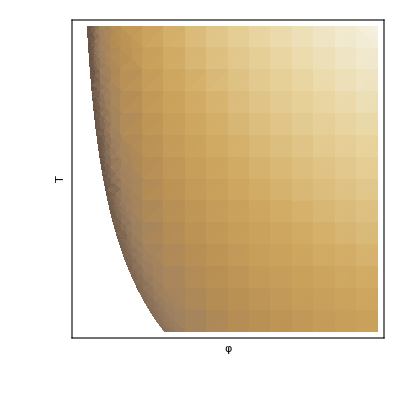

```mathematica
LogarithmicScaling[x_,min_,max_]:=Log[x/min]/Log[max/min]
LogScaleLegend[min_,max_,colorfunction_,height_: 400]:=Module[{bareTicksList,numberedTicks,m,M,ml,Ml,minInArbitraryScale,maxInArbitraryScale,linearScaling},bareTicksList=First[Ticks/.AbsoluteOptions[LogLogPlot[x,{x,min,max}]]];
numberedTicks=(Select[bareTicksList/.{Superscript->Power},NumberQ[#[[2]]]&])[[All,{1,2}]];
m=Min[numberedTicks[[All,2]]];
M=Max[numberedTicks[[All,2]]];
ml=Min[numberedTicks[[All,1]]];
Ml=Max[numberedTicks[[All,1]]];
{minInArbitraryScale,maxInArbitraryScale}=ml+(Ml-ml) Log[{min,max}/m]/Log[M/m];
linearScaling[x_]:=(x-minInArbitraryScale)/(maxInArbitraryScale-minInArbitraryScale);
DensityPlot[y,{x,0,0.04},{y,0,1},AspectRatio->Automatic,PlotRangePadding->0,ImageSize->{Automatic,height},ColorFunction->colorfunction,FrameTicks->{{None,Select[Table[{linearScaling[r[[1]]],r[[2]]/.{Superscript[10.,n_]->Superscript[10,n]},{0,If[r[[2]]==="",0.15,0.3]},{If[r[[2]]==="",Thickness[0.03],Thickness[0.06]]}},{r,bareTicksList}],(#[[1]] (1-#[[1]])≥0&)]},{None,None}}]]
plotter[min_,max_,NumberOfTicks_]:=DensityPlot[SC3ecox/.dM->dMx/.testparam,{φ,0,0.2},{x,0,40},AxesLabel->{"φ","T"},
RegionFunction->Function[{φ,x,z},Evaluate[Im[M3ecoxφ]==0&&M3ecoxφ>0&&COND1xφ>0&&COND2xφ>0&&COND3xφ>0&&COND4xφ>0]],
PlotRange->Full,ColorFunctionScaling->False,FrameTicks->None,ColorFunction->(ColorData["CoffeeTones"][LogarithmicScaling[#,min,max]]&),
PlotLegends->LogScaleLegend[min,max,ColorData["CoffeeTones"],350,LegendLabel->"C"]]
plotter[600,10,5]
```

```mathematica
{{"0.03309","27.43"}}
```

```mathematica
SC3ecox/.dM->dMx/.testparam/.φ->0.03309/.x->27.43
```

143.36

## Figure 1c

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
COND1paramT0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
COND2paramT0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
COND3paramT0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
COND4paramT0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0/.testparam;
M3ecoparamT0=M3ecox/.dM->dMx/.x->T0/.testparam;
COND1paramT1=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
COND2paramT1=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
COND3paramT1=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
COND4paramT1=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.dM->dMx/.x->T0+5/.testparam;
M3ecoparamT1=M3ecox/.dM->dMx/.x->T0+5/.testparam;
```

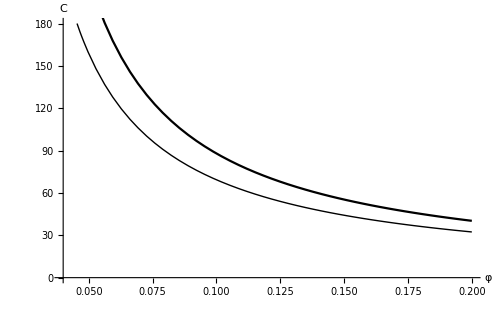

```mathematica
Plot1a=Plot[SC3ecox/.dM->dMx/.x->T0+5/.testparam,{φ,0.04,0.2},PlotRange->{{0.04,0.2},{0,180}},AxesOrigin->{0.04,0},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT1]==0&&M3ecoparamT1>0&&COND1paramT1>0&&COND2paramT1>0&&COND3paramT1>0&&COND4paramT1>0]],
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","C"}];
Plot1b=Plot[SC3ecox/.dM->dMx/.x->T0/.testparam,{φ,0.04,0.2},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT0]==0&&M3ecoparamT0>0&&COND1paramT0>0&&COND2paramT0>0&&COND3paramT0>0&&COND4paramT0>0]],
PlotStyle->{{Black}}];
Show[Plot1a,Plot1b]
```

## Work on Figure 2 - 2.0

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
```

#### No ColorFunctionScaling -- NOT WANTED --

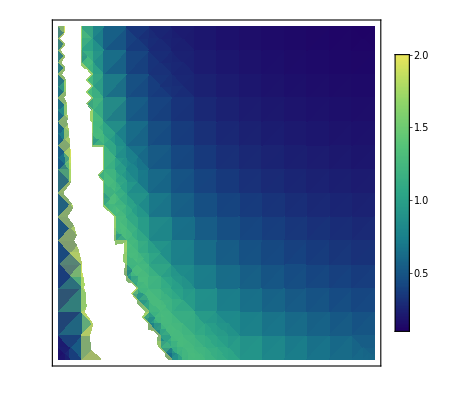

```mathematica
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],
FrameTicks->None,
PlotLegends->Automatic]
```

#### ColorFunctionScaling = True -- NOT WANTED --

```mathematica
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],
ColorFunctionScaling->True,
FrameTicks->None,
PlotLegends->Automatic]
```

-Graphics-

#### ColorFunctionScaling = False

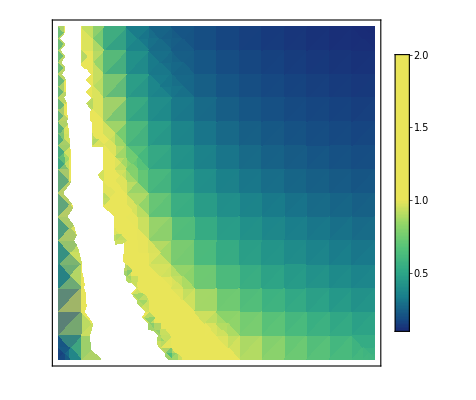

```mathematica
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],
ColorFunctionScaling->False,
FrameTicks->None,
PlotLegends->Automatic]
```

#### Without {0,1} (20 sec)

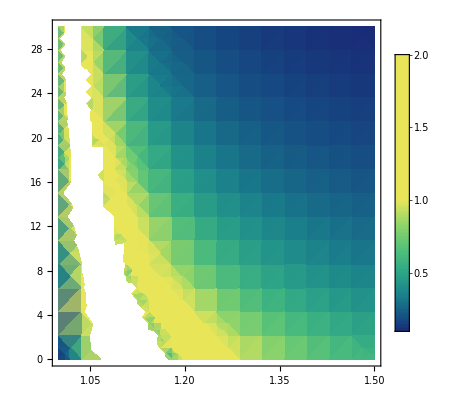

```mathematica
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

#### Without {0,1} and ColorFunctionScaling -- NOT WANTED --

```mathematica
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->"BlueGreenYellow",
FrameTicks->None,
PlotLegends->Automatic]
```

-Graphics-

#### New EVO -- TOO SLOW -- It works if I start c at 1.3

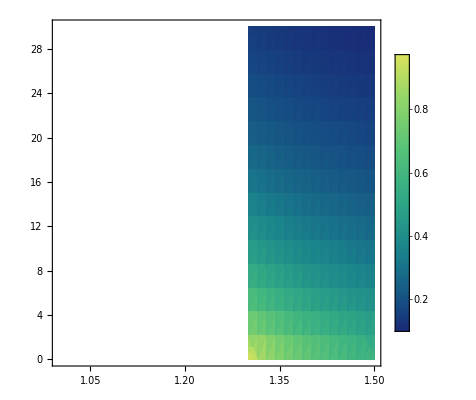

```mathematica
DensityPlot[(NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}])/NIntegrate[ΔSCecodM,{x,x0,x0+5}],
{c,1.3,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{-2,2}},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

#### What’s EVO when c < 1.3

```mathematica
{{"1.097","2.41"}}
```

```mathematica
NIntegrate[ΔSCecoevodM/.c->1.097/.x0->2.41,{x,2.41,7.41}]
```

375.105

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

#### Only 1 NIntegrate

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.503991447201227}. NIntegrate obtained -11394.2+7457.91 ⅈ and 0.0213942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.502340743483281}. NIntegrate obtained -11202.+4432.89 ⅈ and 0.0319594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.503331912706438}. NIntegrate obtained -11175.4+2396.78 ⅈ and 0.0137108 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

#### With Abs[]

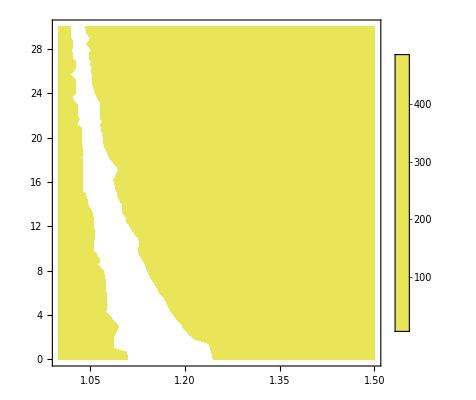

```mathematica
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

#### WorkingPrecision = MachinePrecision

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5},AccuracyGoal->Automatic,PrecisionGoal->Automatic,WorkingPrecision->MachinePrecision],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.503991447201227}. NIntegrate obtained -11394.2+7457.91 ⅈ and 0.0213942 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.502340743483281}. NIntegrate obtained -11202.+4432.89 ⅈ and 0.0319594 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.503331912706438}. NIntegrate obtained -11175.4+2396.78 ⅈ and 0.0137108 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

#### WorkingPrecision = 12

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5},AccuracyGoal->2,WorkingPrecision->2],
{c,1,3/2},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

$Aborted

#### Principal Value = True

```mathematica
DensityPlot[N@Integrate[ΔSCecoevodM,{x,x0,x0+5},PrincipalValue->True],
{c,1.3,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

$Aborted

#### Exclusions

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5},Exclusions->1/ΔSCecoevodM==0,AccuracyGoal->5,MinRecursion->8],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

$Aborted

```mathematica
Block[{x=0,y=0,z=1+I},NIntegrate[Exp[-(xx^2+yy^2+zz^2)]/Sqrt[(xx-x)^2+(yy-y)^2+(zz-z)^2],{xx,-∞,∞},{yy,-∞,∞},{zz,-∞,∞}]]
```

```mathematica
Block[{x=0,y=0,z=1+I},NIntegrate[Exp[-(xx^2+yy^2+zz^2)]/Sqrt[(xx-x)^2+(yy-y)^2+(zz-z)^2],{xx,-∞,∞},{yy,-∞,∞},{zz,-∞,∞},Exclusions->(xx-x)^2+(yy-y)^2+(zz-z)^2==0]]
```

```mathematica
NIntegrate[ΔSCecoevodM/.x0->10,{x,10,15}]
```

```mathematica
Integrate[1/x,{x,-1,2}]
```

Integrate::idiv: Integral of 1/x does not converge on {-1,2}.

∫_-1^2 1/x ⅆx

```mathematica
Integrate[1/x,{x,-1,2},PrincipalValue->True]
```

Log[2]

```mathematica
NIntegrate[1/x,{x,-1,2},PrincipalValue->True]
```

NIntegrate::pvrng: Singular points must be specified in the integration range in order to use PrincipalValue.

```mathematica
N@Integrate[1/x,{x,-1,2},PrincipalValue->True]
```

0.693147

#### Exclusions and PrincipalValue -- PrincipalValue can only be used for 1D integrale --

```mathematica
DensityPlot[N@Integrate[ΔSCecoevodM,{x,x0,x0+5},PrincipalValue->True],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

$Aborted

```mathematica
N@Integrate[ΔSCecoevodM/.c->1.2/.x0->10,{x,10,15},PrincipalValue->True]
```

$Aborted

```mathematica
NIntegrate[ΔSCecoevodM/.c->1.2/.x0->10,{x,10,15}]
```

-87.9667

#### Plot 2D

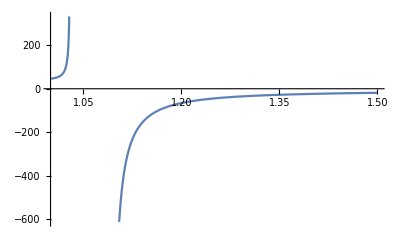

```mathematica
Plot[ΔSCecoevodM/.x0->10/.x->30,{c,1,1.5}]
```

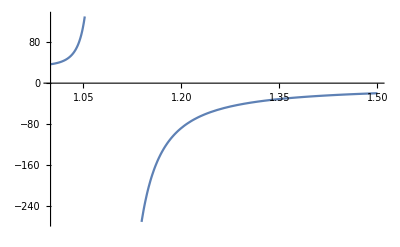

```mathematica
Plot[NIntegrate[ΔSCecoevodM/.x0->10,{x,10,15}],{c,1,1.5}]
```

#### Piecewise sur EVO

```mathematica
delta=.001;
pw=Piecewise[{{1,1/ΔSCecoevodM>delta}},0];
```

```mathematica
DensityPlot[NIntegrate[1+ΔSCecoevodM*pw,{x,x0,x0+5}],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

$Aborted

```mathematica
((1+E^(2*(1-cx)))^(-1)-(1+E^(2*(1-cy)))^(-1))/(2*(1-cx)-2*(1-cy))^2
```

(1/(1+ⅇ^(2 (1-cx)))-1/(1+ⅇ^(2 (1-cy))))/(2 (1-cx)-2 (1-cy))^2

#### Stack example with Piecewise

```mathematica
a=1;
b=1;
beta=1;
eps[x_]:=2*(a-b*Cos[x])
n[x_]:=1/(1+Exp[beta*eps[x]])
delta=.001;
pw[x_,y_]:=Piecewise[{{1,Abs[Abs[x]-Abs[y]]>delta}},0]
NIntegrate[1+Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2*pw[Cos[x],Cos[y]],{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.4794 and 0.459541 for the integral and error estimates.

1.00003

#### Sans fonctions de -- MARCHE PAS --

```mathematica
a=1;
b=1;
beta=1;
delta=.001;
pw=Piecewise[{{1,Abs[Abs[Cos[x]]-Abs[Cos[y]]]>delta}},0]
NIntegrate[1+Cos[(x+y)/2]^2*(1/(1+Exp[beta*2*(a-b*Cos[x])])-1/(1+Exp[beta*eps[y]]))/(2*(a-b*Cos[x])-2*(a-b*Cos[y]))^2*pw,{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

Piecewise[{{1, Abs[Abs[Cos[x]]-Abs[Cos[y]]]>0.001}, {0, True}}]

NIntegrate::inumr: The integrand 1+((1/(1+ⅇ^(2 Plus[«2»]))-1/(1+ⅇ^eps[«1»])) Cos[(x+y)/2]^2 (Piecewise[{{1, Abs[Plus[«2»]]>0.001}, {0, True}}]))/(2 (1-Cos[«1»])-2 (1-Cos[«1»]))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-3.14159,0.},{-3.14159,3.14159}}.

NIntegrate[1+(Cos[(x+y)/2]^2 (1/(1+Exp[beta 2 (a-b Cos[x])])-1/(1+Exp[beta eps[y]])) pw)/(2 (a-b Cos[x])-2 (a-b Cos[y]))^2,{x,-π,π},{y,-π,π}]/(4 π^2)

#### Final

```mathematica
NIntegrate[1+Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2*pw[Cos[x],Cos[y]],{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 39.4794 and 0.459541 for the integral and error estimates.

1.00003

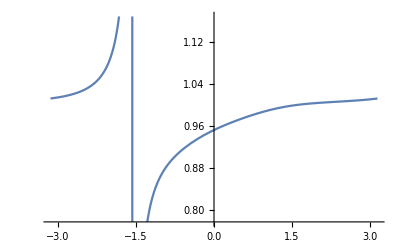

```mathematica
Plot[1+Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2*pw[Cos[x],Cos[y]]/.x->Pi/2,{y,-Pi,Pi}]
```

#### Je retire +1

```mathematica
NIntegrate[Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2*pw[Cos[x],Cos[y]],{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -0.0000104178 and 0.0000725988 for the integral and error estimates.

-2.63887×10^-7

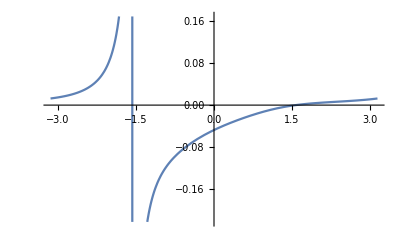

```mathematica
Plot[Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2*pw[Cos[x],Cos[y]]/.x->Pi/2,{y,-Pi,Pi}]
```

#### Je retire pw

```mathematica
NIntegrate[1+Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2,{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in y near {x,y} = {2.16219,0.0000202323}. NIntegrate obtained 5.24689×10^6 and 767984. for the integral and error estimates.

132905.

```mathematica
pw[Cos[x],Cos[y]]
```

Piecewise[{{1, Abs[Abs[Cos[x]]-Abs[Cos[y]]]>0.001}, {0, True}}]

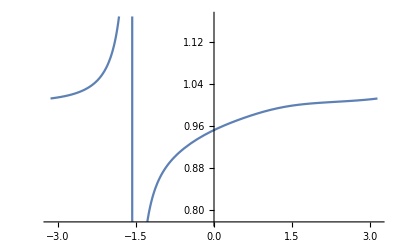

```mathematica
Plot[1+Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2/.x->Pi/2,{y,-Pi,Pi}]
```

#### Je retire +1 et *pw

```mathematica
NIntegrate[Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2,{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0000202323,2.16219}. NIntegrate obtained -5.24686×10^6 and 767984. for the integral and error estimates.

-132904.

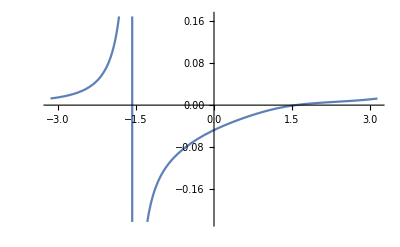

```mathematica
Plot[Cos[(x+y)/2]^2*(n[x]-n[y])/(eps[x]-eps[y])^2/.x->Pi/2,{y,-Pi,Pi}]
```

```mathematica
((1+E^(2*(1-cx)))^(-1)-(1+E^(2*(1-cy)))^(-1))/(2*(1-cx)-2*(1-cy))^2
```

```mathematica
NIntegrate[((1+E^(2*(1-cx)))^(-1)-(1+E^(2*(1-cy)))^(-1))/(2*(1-cx)-2*(1-cy))^2,{x,-Pi,Pi},{y,-Pi,Pi}]/(4*Pi^2)
```

NIntegrate::inumr: The integrand (1/(1+ⅇ^(2 (1+Times[«2»])))-1/(1+ⅇ^(2 Plus[«2»])))/(2 (1-cx)-2 (1-cy))^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,3.14159},{0,3.14159}}.

NIntegrate[(1/(1+ⅇ^(2 (1-cx)))-1/(1+ⅇ^(2 (1-cy))))/(2 (1-cx)-2 (1-cy))^2,{x,-π,π},{y,-π,π}]/(4 π^2)

#### c = 1.3-1.5

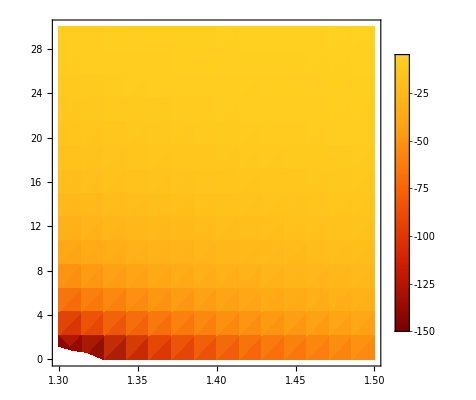

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}],
{c,1.3,1.5},{x0,0,30},
PlotRange->{{1.3,1.5},{0,30},{-150,0}},
ColorFunction->"SolarColors",
ColorFunctionScaling->True,
PlotLegends->Automatic]
```

```mathematica
{{"1.393","10."}}=jaune-orange
```

```mathematica
NIntegrate[ΔSCecoevodM/.c->1.4/.x0->10,{x,10,15}]
```

-25.8865

```mathematica
{{"1.313","1.488"}} = blanc
```

```mathematica
NIntegrate[ΔSCecoevodM/.c->1.313/.x0->1.488,{x,1.488,6.488}]
```

-125.197

#### Maybe RegionFunction slows down but prevent the error

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}],
{c,1,1.5},{x0,0,30},
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.33139071590133}. NIntegrate obtained 1628.89-320.745 ⅈ and 0.366602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.33186029159865180516997273940660306834615767002105712890625}. NIntegrate obtained 1444.46-28.1314 ⅈ and 0.10837 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.331336059251933275071611006978855584748089313507080078125}. NIntegrate obtained 1395.07-3.4411 ⅈ and 0.307238 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

```mathematica
DensityPlot[Integrate[ΔSCecoevodM,{x,x0,x0+5},PrincipalValue->True],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

$Aborted

```mathematica
NIntegrate[f[x],{x,0,1,3},Method->PrincipalValue,AccuracyGoal->10]
```

NIntegrate::inumr: The integrand f[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,0.5}}.

NIntegrate::inumr: The integrand f[x] has evaluated to non-numerical values for all sampling points in the region with boundaries {{1.5,3}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[f[x],{x,0,1,3},Method→PrincipalValue,AccuracyGoal→10]

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5},Method->PrincipalValue,AccuracyGoal->10],
{c,1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

NIntegrate::pvrng: Singular points must be specified in the integration range in order to use PrincipalValue.

General::stop: Further output of NIntegrate::pvrng will be suppressed during this calculation.

-Graphics-

#### 1 NIntegrate + GaussKronrodRule

```mathematica
DensityPlot[NIntegrate[ΔSCecoevodM,{x,x0,x0+5},AccuracyGoal->10,Method->"GaussKronrodRule"],
{c,1.1,1.5},{x0,0,30},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.60684616883015}. NIntegrate obtained -12080.8+6037.45 ⅈ and 0.0237635 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.48754287468662}. NIntegrate obtained -11826.2+3250.71 ⅈ and 0.0211961 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.44400633025050197273675411935300871846266090869903564453125}. NIntegrate obtained -11772.9+1565.11 ⅈ and 0.0540142 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

$Aborted

#### Coordinates

```mathematica
12.18+5
```

17.18

```mathematica
{{"1.158","12.18"}}
```

```mathematica
(NIntegrate[ΔSCecoevodM/.c->1.158/.x0->12.18,{x,12.18,17.18}]-NIntegrate[ΔSCecodM/.c->1.158/.x0->12.18,{x,12.18,17.18}])/NIntegrate[ΔSCecodM/.c->1.158/.x0->12.18,{x,12.18,17.18}]
```

0.782475

```mathematica
{{"1.355","10.85"}}
```

```mathematica
(NIntegrate[ΔSCecoevodM/.c->1.355/.x0->10.85,{x,10.85,15.85}]-NIntegrate[ΔSCecodM/.c->1.355/.x0->10.85,{x,10.85,15.85}])/NIntegrate[ΔSCecodM/.c->1.355/.x0->10.85,{x,10.85,15.85}]
```

0.372297

#### GaussKronrodRule

```mathematica
AccuracyGoal->10,Method->"GaussKronrodRule"
```

```mathematica
DensityPlot[(NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}])/NIntegrate[ΔSCecodM,{x,x0,x0+5}],
{c,1.3,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{-2,2}},
ColorFunction->"BlueGreenYellow",
ColorFunctionScaling->False,
PlotLegends->Automatic]
```

#### Calculations

```mathematica
ΔSCecoevodM/.c->1.2/.x0->20/.x->25
```

-10.4697

```mathematica
NIntegrate[ΔSCecoevodM/.c->1.2/.x0->20,{x,20,25}]
```

-28.0232

```mathematica
Abs[NIntegrate[ΔSCecoevodM/.c->1.2/.x0->20,{x,20,25}]-NIntegrate[ΔSCecodM/.c->1.2/.x0->20,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM/.c->1.2/.x0->20,{x,20,25}]]
```

0.35649

```mathematica
(NIntegrate[ΔSCecoevodM/.c->1.2/.x0->7.999020887797093,{x,7.999020887797093,12.999020887797094}]-NIntegrate[ΔSCecodM/.c->1.2/.x0->20,{x,7.999020887797093,12.999020887797094}])/NIntegrate[ΔSCecodM/.c->1.2/.x0->20,{x,7.999020887797093,12.999020887797094}]
```

-2.0722

```mathematica
7.999020887797093+5
```

12.999

#### ThermometerColors

## Test Figure 2 without Abs

```mathematica
testgmdm={eC->10^-6,eD->10^-2,dMref0->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM0->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testgmdm;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testgmdm;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testgmdm;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1gmdm=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND2gmdm=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND3gmdm=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND4gmdm=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
M3ecogmdm=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
```

```mathematica
{{"0.2351","0.0003959"}}
```

```mathematica
Abs[NIntegrate[ΔSCecoevodM/.γM->0.2351/.dMref->0.0003959,{x,20,25}]-NIntegrate[ΔSCecodM/.γM->0.2351/.dMref->0.0003959,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM/.γM->0.2351/.dMref->0.0003959,{x,20,25}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {21.4062}. NIntegrate obtained -12839.9-1733.2 ⅈ and 3.55897 for the integral and error estimates.

707.066

```mathematica
(NIntegrate[ΔSCecoevodM/.γM->0.2351/.dMref->0.0003959,{x,20,25}]-NIntegrate[ΔSCecodM/.γM->0.2351/.dMref->0.0003959,{x,20,25}])/NIntegrate[ΔSCecodM/.γM->0.2351/.dMref->0.0003959,{x,20,25}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {21.4062}. NIntegrate obtained -12839.9-1733.2 ⅈ and 3.55897 for the integral and error estimates.

-700.729-94.4534 ⅈ

```mathematica
Im[M3ecogmdm]/.γM->0.1995/.dMref->0.0005522
```

0

```mathematica
M3ecogmdm/.γM->0.1995/.dMref->0.0005522
```

-0.0369427

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {20.122088082163}. NIntegrate obtained -0.0000794842 and 4.95159×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {20.2707233307823}. NIntegrate obtained -6162.9+2480.39 ⅈ and 0.0654436 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

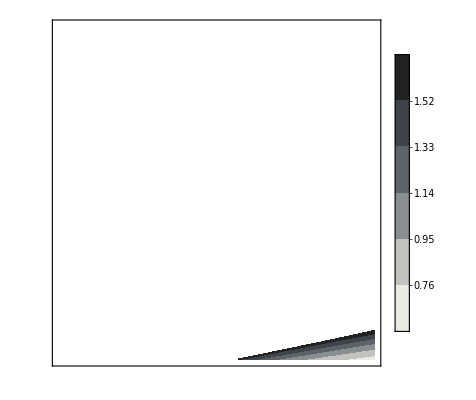

```mathematica
ContourPlot[(NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}])/NIntegrate[ΔSCecodM,{x,20,25}],
{γM,0,0.3},{dMref,2 10^-4,2 10^-3},
RegionFunction->Function[{γM,dMref,z},Evaluate[Im[M3ecogmdm]==0&&M3ecogmdm>0&&COND1gmdm>0&&COND2gmdm>0&&COND3gmdm>0&&COND4gmdm>0]],
PlotRange->{{0,0.3},{2 10^-4,2 10^-3},{-2,2}},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
Contours->20,
ContourStyle->None,
ColorFunctionScaling->True,
FrameTicks->None,
PlotLegends->Automatic]
```

## Figure 2 - 2.0 - finale

### Figure 2a

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {20.2048455930150598902628189534880220890045166015625}. NIntegrate obtained -0.000168118 and 4.13156×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {23.6425}. NIntegrate obtained -0.000155249 and 4.02239×10^-10 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {20.2480541007720215851417577823667670600116252899169921875}. NIntegrate obtained -0.000144198 and 4.758×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

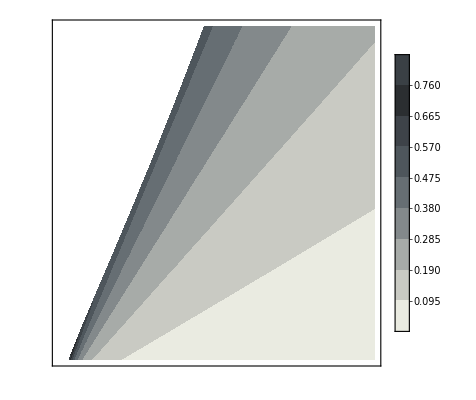

```mathematica
testgmdm={eC->10^-6,eD->10^-2,dMref0->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM0->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testgmdm;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testgmdm;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testgmdm;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1gmdm=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND2gmdm=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND3gmdm=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND4gmdm=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
M3ecogmdm=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{γM,0,0.3},{dMref,2 10^-4,2 10^-3},
RegionFunction->Function[{γM,dMref,z},Evaluate[Im[M3ecogmdm]==0&&M3ecogmdm>0&&COND1gmdm>0&&COND2gmdm>0&&COND3gmdm>0&&COND4gmdm>0]],
PlotRange->{{0,0.3},{2 10^-4,2 10^-3},{0,2}},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
Contours->20,
ContourStyle->None,
ColorFunctionScaling->True,
FrameTicks->None,
PlotLegends->Automatic]
```

### Calculs et Plots 2D

```mathematica
{{"0.2311","0.0004599"}}
```

```mathematica
1000-1)/1
```

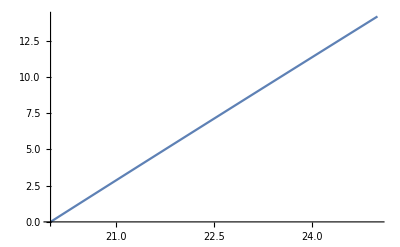

```mathematica
Plot[ΔSCecodMN,{x,20,25}]
```

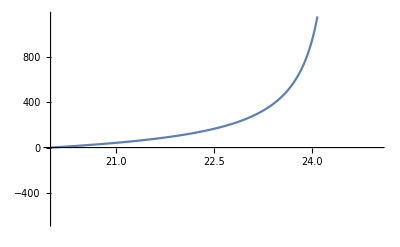

```mathematica
Plot[ΔSCecoevodMN,{x,20,25}]
```

```mathematica
NIntegrate[ΔSCecoevodMN,{x,20,24}]
```

744.352

```mathematica
(-2446.6829464046546-14.178655956683542)/14.178655956683542
```

-173.561

```mathematica
ΔSCecoevodM/.γM->0.2311/.dMref->0.0004599/.x->25
```

-2446.68

```mathematica
ΔSCecodM/.γM->0.2311/.dMref->0.0004599/.x->25
```

14.1787

```mathematica
SC3ecodMx/.γM->0.2311/.dMref->0.0004599/.x->25
```

4778.39

```mathematica
SC3adaptT0/.γM->0.2311/.dMref->0.0004599
```

4764.21

```mathematica
SC3ecoevodMx/.γM->0.2311/.dMref->0.0004599/.x->25
```

2317.53

```mathematica
ΔSCecoevodMN=ΔSCecoevodM/.γM->0.2311/.dMref->0.0004599;
ΔSCecodMN=ΔSCecodM/.γM->0.2311/.dMref->0.0004599;
Abs[NIntegrate[ΔSCecoevodMN,{x,20,25}]-NIntegrate[ΔSCecoevodMN,{x,20,25}]]/Abs[NIntegrate[ΔSCecoevodMN,{x,20,25}]]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {24.3749}. NIntegrate obtained 818.517-1701.76 ⅈ and 1.98185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {24.3749}. NIntegrate obtained 818.517-1701.76 ⅈ and 1.98185 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {24.3749}. NIntegrate obtained 818.517-1701.76 ⅈ and 1.98185 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.

### Figure 2b

```mathematica
testEvUV0U={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU00->10^5,EvU0->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testEvUV0U;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testEvUV0U;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testEvUV0U;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1EvV0U=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND2EvV0U=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND3EvV0U=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND4EvV0U=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
M3ecoEvV0U=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
```

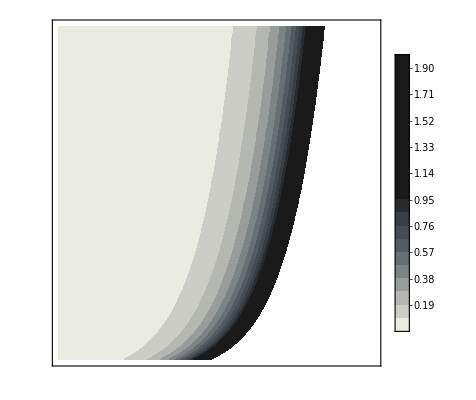

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{EvU,30,50},{VmU0,10^5,2 10^6},
PlotRange->{{30,50},{10^5,2 10^6},{0,2}},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
RegionFunction->Function[{EvU,VmU0,z},Evaluate[Im[M3ecoEvV0U]==0&&M3ecoEvV0U>0&&COND1EvV0U>0&&COND2EvV0U>0&&COND3EvV0U>0&&COND4EvV0U>0]],
Contours->20,
ContourStyle->None,
ColorFunctionScaling->False,
FrameTicks->None,
PlotLegends->Automatic]
```

### Figure 2c = Figure 2d avec gM=0.09 et dM=1.1e-3

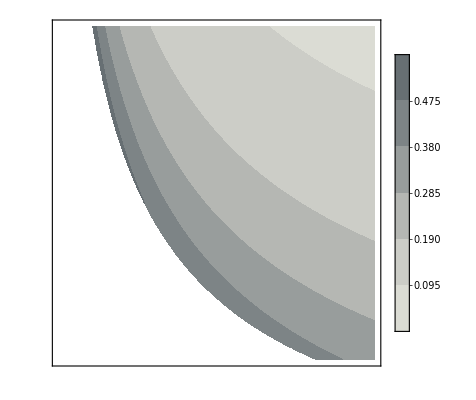

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->1.1 10^-3,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.09,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
Contours->20,
ContourStyle->None,
ColorFunctionScaling->False,
FrameTicks->None,
PlotLegends->Automatic]
```

### Figure 2d

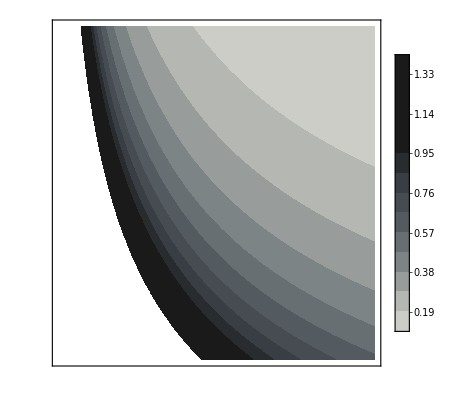

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
PlotRange->{{1,1.5},{0,30},{0,2}},
ColorFunction->(ColorData["GrayTones",(1-#)]&),
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
Contours->20,
ContourStyle->None,
ColorFunctionScaling->False,
FrameTicks->None,
PlotLegends->Automatic]
```

## Figure 2 (a-d)

### Figure 2b

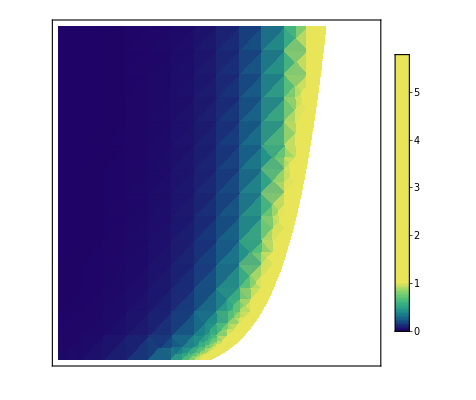

```mathematica
testEvUV0U={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU00->10^5,EvU0->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testEvUV0U;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testEvUV0U;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testEvUV0U;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1EvV0U=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND2EvV0U=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND3EvV0U=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND4EvV0U=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
M3ecoEvV0U=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{EvU,30,50},{VmU0,10^5,2 10^6},
RegionFunction->Function[{EvU,VmU0,z},Evaluate[Im[M3ecoEvV0U]==0&&M3ecoEvV0U>0&&COND1EvV0U>0&&COND2EvV0U>0&&COND3EvV0U>0&&COND4EvV0U>0]],
PlotRange->Full,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],ColorFunctionScaling->False,FrameTicks->None,PlotLegends->Automatic]
```

### Figure 2d

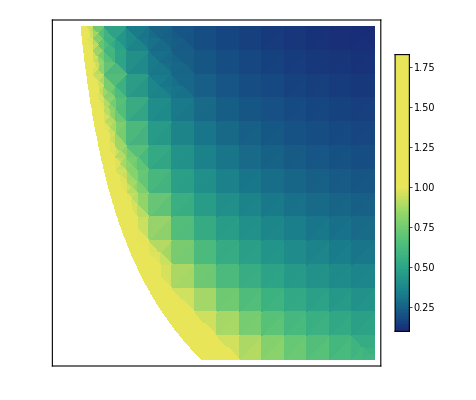

```mathematica
testT0c0={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->0,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c0->1.1131,x00->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testT0c0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testT0c0;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testT0c0;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1T0c0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND2T0c0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND3T0c0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
COND4T0c0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
M3ecoT0c0=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testT0c0;
DensityPlot[Abs[NIntegrate[ΔSCecoevodM,{x,x0,x0+5}]-NIntegrate[ΔSCecodM,{x,x0,x0+5}]]/Abs[NIntegrate[ΔSCecodM,{x,x0,x0+5}]],
{c,1,1.5},{x0,0,30},
RegionFunction->Function[{c,x0,z},Evaluate[Im[M3ecoT0c0]==0&&M3ecoT0c0>0&&COND1T0c0>0&&COND2T0c0>0&&COND3T0c0>0&&COND4T0c0>0]],
PlotRange->Full,ColorFunction->ColorData[{"BlueGreenYellow",{0,1}}],ColorFunctionScaling->False,FrameTicks->None,PlotLegends->Automatic]
```

## New figure 3 - TEST

116.68

40.3494

22.4482

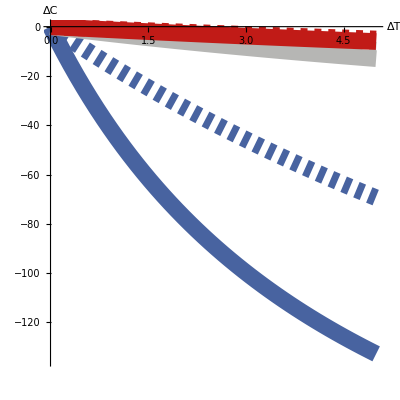

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-135,0}},
PlotStyle->{{RGBColor["#4863A0"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#4863A0"],Thickness[0.03]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#B6B6B4"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#C11B17"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

### DeltaC(T) par scenario

## Figure 3 - 2.0 - thick

#### Figure 3a

116.68

40.3494

22.4482

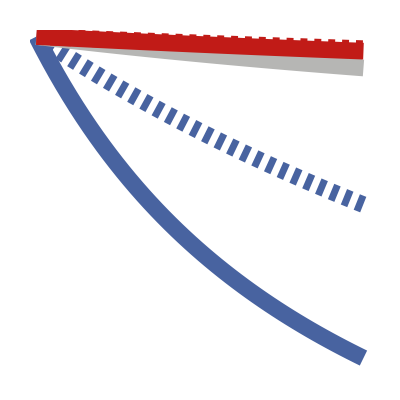

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-135,0}},
PlotStyle->{{RGBColor["#4863A0"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#4863A0"],Thickness[0.03]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#B6B6B4"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#C11B17"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3b

21.4137

15.5178

12.6649

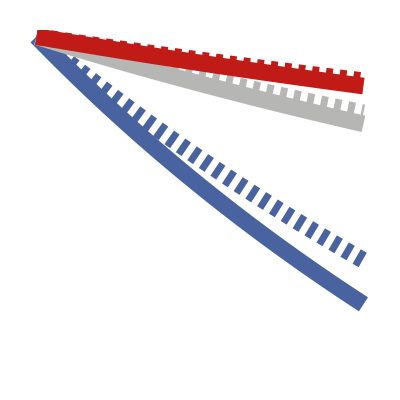

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-40,0}},PlotStyle->{{RGBColor["#4863A0"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#4863A0"],Thickness[0.03]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#B6B6B4"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#C11B17"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3c

13.6124

23.7831

34.8103

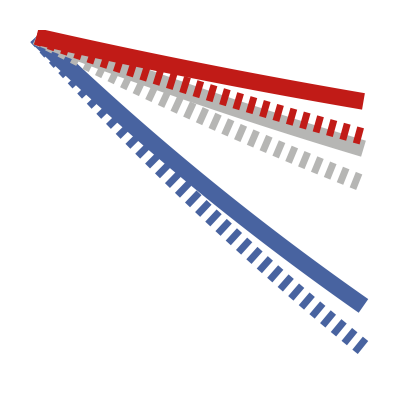

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-20,0}},PlotStyle->{{RGBColor["#4863A0"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#4863A0"],Thickness[0.03]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#B6B6B4"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#C11B17"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3d

83.0005

6.73921

140.856

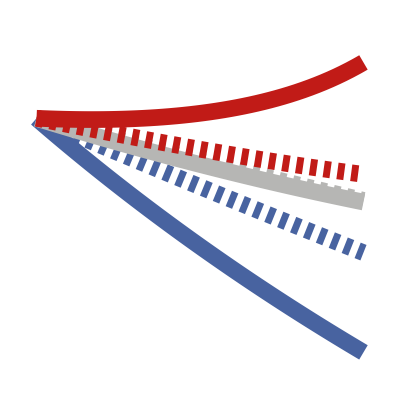

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-15,5}},PlotStyle->{{RGBColor["#4863A0"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#4863A0"],Thickness[0.03]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#B6B6B4"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],CapForm["Butt"],Dashed,Thickness[0.03]},{RGBColor["#C11B17"],Thickness[0.03]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

## Figure 3 - 2.0 Lapis blue = #15317E Chili red = #C11B17

#### Figure 3a

116.68

40.3494

22.4482

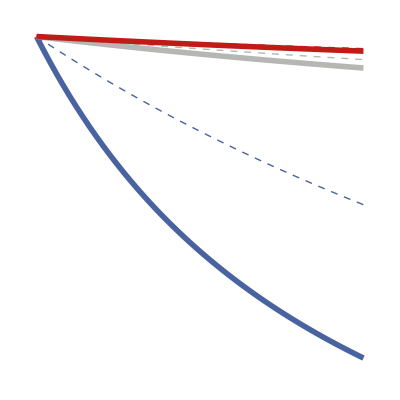

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-135,0}},
PlotStyle->{{RGBColor["#4863A0"],Dashed,Thick},{RGBColor["#4863A0"],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],Dashed,Thick},{RGBColor["#B6B6B4"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],Dashed,Thick},{RGBColor["#C11B17"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3a - IN

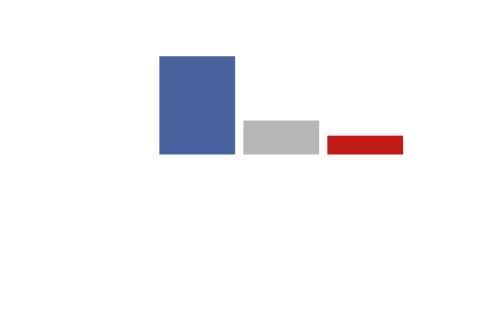

```mathematica
BarChart[{{116.7,40.3,22.4}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{{RGBColor["#4863A0"],RGBColor["#B6B6B4"],RGBColor["#C11B17"]}},
ImageSize->500,AxesLabel->None, Axes->None,ChartBaseStyle->EdgeForm[None]]
```

### Figure 3b

21.4137

15.5178

12.6649

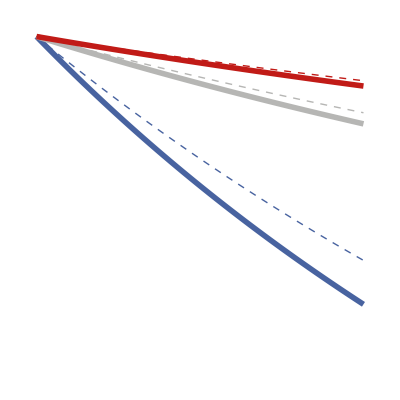

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-40,0}},PlotStyle->{{RGBColor["#4863A0"],Dashed,Thick},{RGBColor["#4863A0"],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],Dashed,Thick},{RGBColor["#B6B6B4"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],Dashed,Thick},{RGBColor["#C11B17"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3b - IN

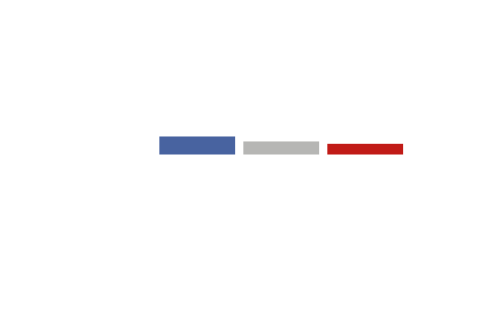

```mathematica
BarChart[{{21.4,15.5,12.7}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{{RGBColor["#4863A0"],RGBColor["#B6B6B4"],RGBColor["#C11B17"]}},
ImageSize->500,AxesLabel->None, Axes->None,ChartBaseStyle->EdgeForm[None]]
```

### Figure 3c

13.6124

23.7831

34.8103

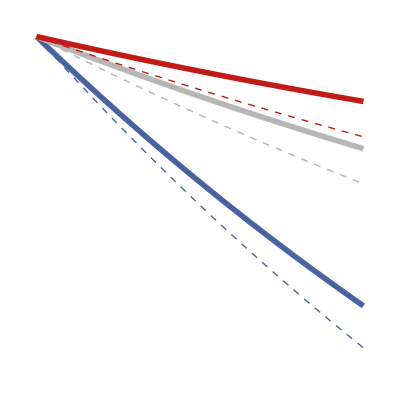

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-20,0}},PlotStyle->{{RGBColor["#4863A0"],Dashed,Thick},{RGBColor["#4863A0"],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],Dashed,Thick},{RGBColor["#B6B6B4"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],Dashed,Thick},{RGBColor["#C11B17"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3c - IN

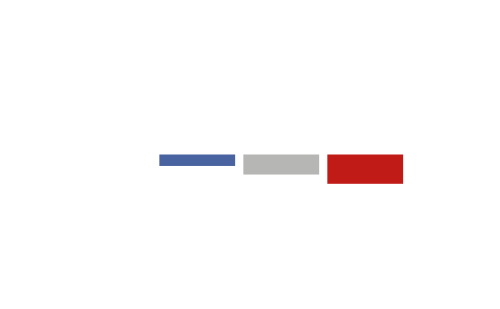

```mathematica
BarChart[{{-13.6,-23.8,-34.8}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{{RGBColor["#4863A0"],RGBColor["#B6B6B4"],RGBColor["#C11B17"]}},
ImageSize->500,AxesLabel->None, Axes->None,ChartBaseStyle->EdgeForm[None]]
```

### Figure 3d

83.0005

6.73921

140.856

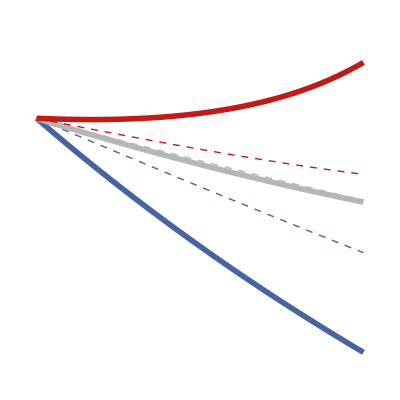

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-15,5}},PlotStyle->{{RGBColor["#4863A0"],Dashed,Thick},{RGBColor["#4863A0"],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{RGBColor["#B6B6B4"],Dashed,Thick},{RGBColor["#B6B6B4"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{RGBColor["#C11B17"],Dashed,Thick},{RGBColor["#C11B17"],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9,AxesLabel->None, Axes->None]
```

### Figure 3d - IN

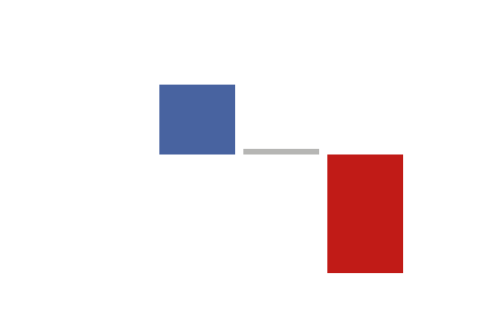

```mathematica
BarChart[{{83,6.7,-140.9}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{{RGBColor["#4863A0"],RGBColor["#B6B6B4"],RGBColor["#C11B17"]}},
ImageSize->500,AxesLabel->None, Axes->None,ChartBaseStyle->EdgeForm[None]]
```

### Lapis blue = #15317E Granite grey = #837E7C Chili red = #C11B17

## Figure 3 (a-d)

### Figure 3a : EdM:0 (baseline scenario)

116.68

40.3494

22.4482

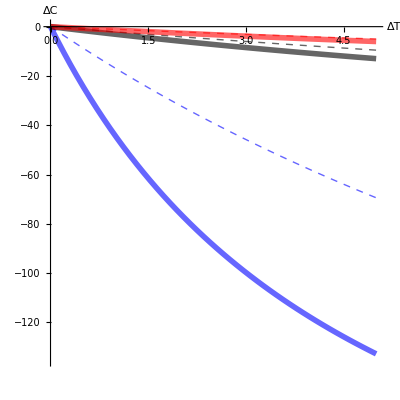

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-135,0}},
PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Red,Dashed,Opacity[0.6],Thick},{Red,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

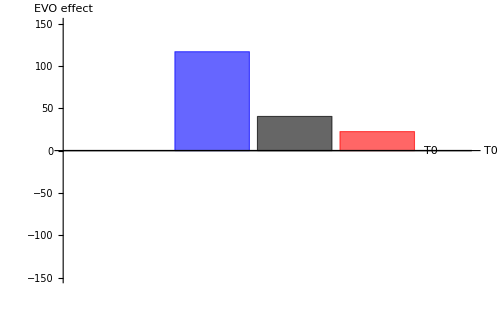

```mathematica
BarChart[{{116.7,40.3,22.4}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"} ]
```

### Figure 3b : EdM=25 (low mortality T-dependence)

21.4137

15.5178

12.6649

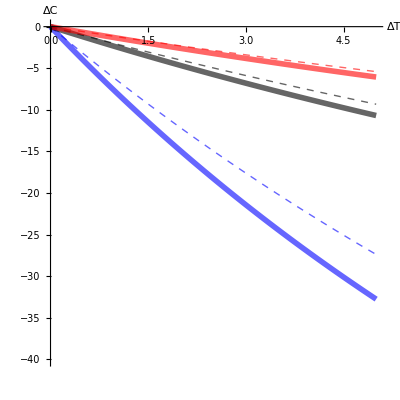

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-40,0}},PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->25};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Red,Opacity[0.6],Dashed,Thick},{Red,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

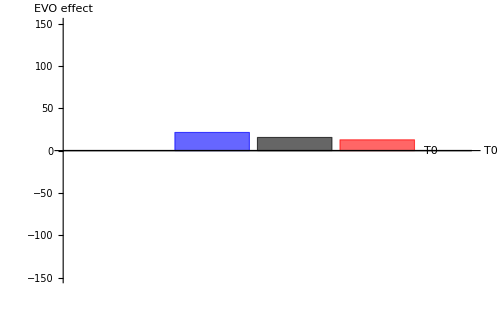

```mathematica
BarChart[{{21.4,15.5,12.7}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"} ]
```

### Figure 3c : EdM=55 (high mortality T-dependence)

13.6124

23.7831

34.8103

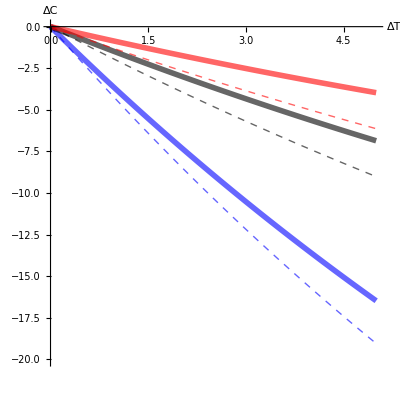

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-20,0}},PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->55};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevodM,{dx,0,5}]-NIntegrate[ΔSCecodM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecodM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecodM,ΔSCecoevodM},{dx,0,5},PlotStyle->{{Red,Opacity[0.6],Dashed,Thick},{Red,Opacity[0.6],Thickness[0.01]}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

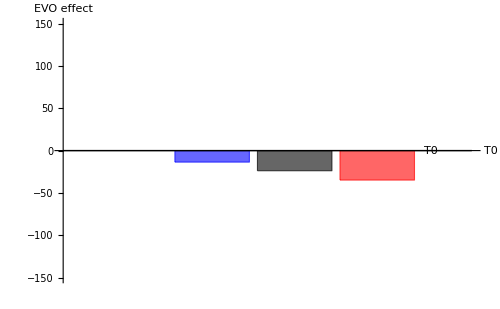

```mathematica
BarChart[{{-13.6,-23.8,-34.8}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"}]
```

### Figure 3d : m= - 0.014 (MGE T-dependence)

83.0005

6.73921

140.856

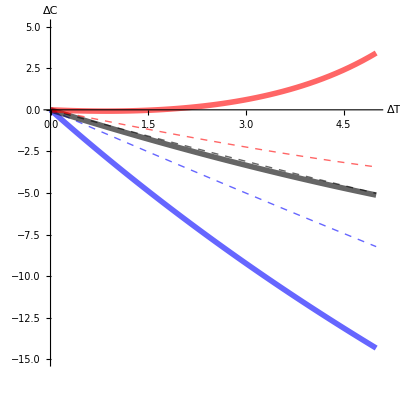

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot3=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-15,5}},PlotStyle->{{Blue,Opacity[0.6],Dashed,Thick},{Blue,Opacity[0.6],Thickness[0.01]}},AspectRatio->1,AxesLabel->{"ΔT","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot6=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{Black,Opacity[0.6],Dashed,Thick},{Black,Opacity[0.6],Thickness[0.01]}},ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γMref->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,m->-0.014};
γMx=γMref+m(T0+dx-xref);
φγMx=φx/.x->T0+dx/.γM->γMx;
φγMT0=φγMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.dx->0/.testparam;
SC3ecoγMx=SC3ecox/.x->T0+dx/.φ->φγMT0/.γM->γMx/.testparam;
SC3ecoevoγMx=SC3ecox/.φ->φx/.x->T0+dx/.γM->γMx/.testparam;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
Abs[NIntegrate[ΔSCecoevoγM,{dx,0,5}]-NIntegrate[ΔSCecoγM,{dx,0,5}]]/Abs[NIntegrate[ΔSCecoγM,{dx,0,5}]]*100
Plot9=Plot[{ΔSCecoγM,ΔSCecoevoγM},{dx,0,5},PlotStyle->{{Red,Opacity[0.6],Dashed,Thick},{Red,Opacity[0.6],Thickness[0.01]}},ImageSize->500];
Show[Plot3,Plot6,Plot9]
```

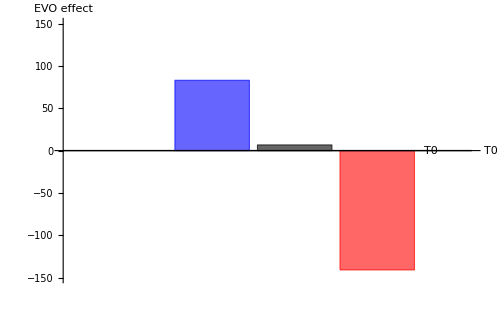

```mathematica
BarChart[{{83,6.7,-140.9}},
AxesOrigin->{0,0},
PlotRange->{Automatic,{-150,150}},
ChartStyle->{Opacity[0.6],{Blue,Black,Red}},
ImageSize->500,AxesLabel->{"T0","EVO effect"}]
```

## Figure 4 (a-d) (ECO)

### Figure 4a - Baseline scenario

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

ReplaceAll::reps: {testpar} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {testAK} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand ΔSCecodM/.testpar/.testAK has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,5}}.

NIntegrate[ΔSCecodM/.γM→γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]

ReplaceAll::reps: {testpar} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {testME} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand ΔSCecodM/.testpar/.testME has evaluated to non-numerical values for all sampling points in the region with boundaries {{5,10}}.

NIntegrate[ΔSCecodM/.γM→γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]

ReplaceAll::reps: {testpar} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {testWV} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand ΔSCecodM/.testpar/.testWV has evaluated to non-numerical values for all sampling points in the region with boundaries {{9,14}}.

NIntegrate[ΔSCecodM/.γM→γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]

ReplaceAll::reps: {testpar} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {testCA} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand ΔSCecodM/.testpar/.testCA has evaluated to non-numerical values for all sampling points in the region with boundaries {{17,22}}.

NIntegrate[ΔSCecodM/.γM→γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]

ReplaceAll::reps: {testpar} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {testCR} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NIntegrate::inumr: The integrand ΔSCecodM/.testpar/.testCR has evaluated to non-numerical values for all sampling points in the region with boundaries {{26,31}}.

NIntegrate[ΔSCecodM/.γM→γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-9.75727

-3.21334

-15.0353

-13.4817

-17.0721

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-5.59079

-2.14822

-9.8245

-9.44123

-12.2572

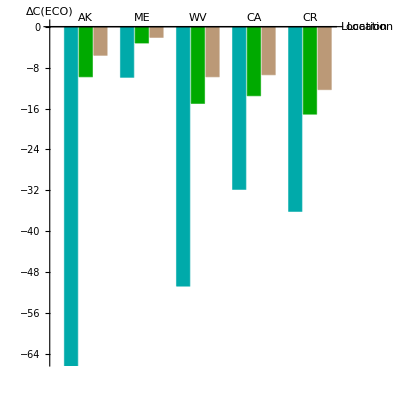

```mathematica
BarChart[{{-170.9,-9.8,-5.6},{-9.9,-3.2,-2.1},{-50.7,-15,-9.8},{-31.8,-13.5,-9.4},{-36.1,-17.1,-12.3}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"}]
```

### Figure 4b - Low mortality T-dependence (EdM = 25)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-15.2163

-5.44244

-32.4465

-29.2713

-38.3475

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-5.49483

-2.44518

-12.3667

-12.7386

-17.4934

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-3.69634

-1.73152

-8.4134

-8.94598

-12.4342

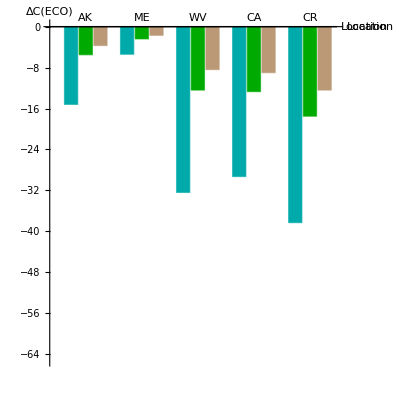

```mathematica
BarChart[{{-15.2,-5.5,-3.7},{-5.4,-2.4,-1.7},{-32.4,-12.4,-8.4},{-29.3,-12.7,-9},{-38.3,-17.5,-12.4}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"}]
```

### Figure 4c - High mortality T-dependence (EdM = 55)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-9.63332

-4.1612

-25.0055

-26.8456

-42.073

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-4.42801

-2.11158

-10.8518

-11.9809

-17.9883

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-3.13527

-1.53933

-7.57721

-8.43361

-12.5596

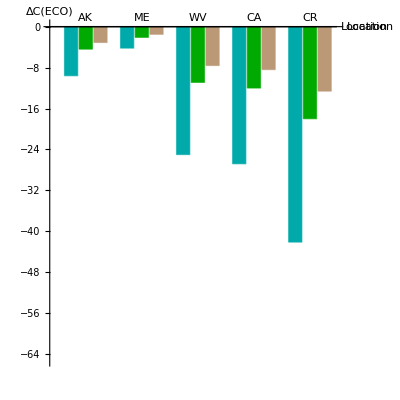

```mathematica
BarChart[{{-9.6,-4.4,-3.1},{-4.2,-2.1,-1.5},{-25,-10.9,-7.6},{-26.8,-12,-8.4},{-42.1,-18,-12.6}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"}]
```

### Figure 4d - MGE T-dependence

```mathematica
γMx=γMref+m(x-xref);
φγMx=φx/.γM->γMx;
φγMT0=φγMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014/.x->x0;
SC3ecoγMx=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014;
SC3ecoevoγMx=SC3ecox/.φ->φx/.γM->γMx/.m->-0.014;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-0.729677

-1.67335

-11.6027

-14.0385

-33.1057

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-0.652151

-0.928154

-5.2073

-6.76087

-14.7635

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-0.711518

-0.754988

-3.9722

-5.10773

-10.5303

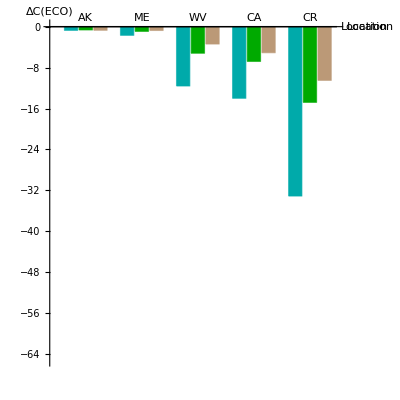

```mathematica
BarChart[{{-0.73,-0.65,-0.71},{-1.7,-0.93,-0.75},{-11.6,-5.2,-3.4},{-14,-6.8,-5.1},{-33.1,-14.8,-10.5}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{20,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECO)"} ]
```

## Figure 4 (e-h) (ECOEVO)

### Figure 4e - Baseline scenario

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-556.028

-24.072

-92.7902

-47.3891

-41.996

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-21.7836

-5.07653

-21.3065

-16.8857

-18.5883

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-10.3186

-3.01212

-12.8012

-11.1972

-13.0723

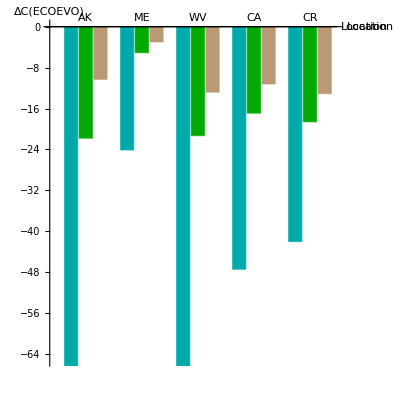

```mathematica
BarChart[{{-556,-21.8,-10.3},{-24.1,-5.1,-3},{-92.8,-21.3,-12.8},{-47.4,-16.9,-11.2},{-42,-18.6,-13.1}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"}]
```

### Figure 4f - Low mortality T-dependence (EdM = 25)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-20.7003

-6.6998

-38.6089

-34.1117

-41.3944

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-6.50917

-2.71754

-13.5996

-13.8228

-18.219

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-4.1998

-1.87175

-9.03621

-9.50865

-12.8166

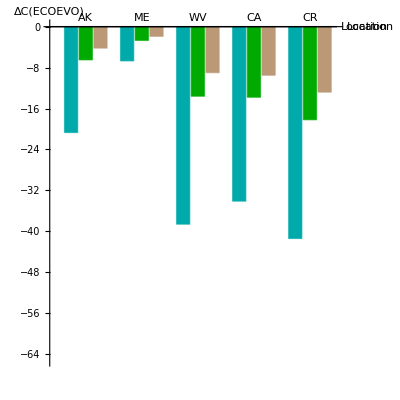

```mathematica
BarChart[{{-20.7,-6.5,-4.2},{-6.7,-2.7,-1.9},{-38.6,-13.6,-9},{-34.1,-13.8,-9.5},{-41.4,-18.2,-12.8}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"}]
```

### Figure 4g - High mortality T-dependence (EdM = 55)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-7.99328

-3.5669

-21.1507

-21.1325

-34.9554

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-4.00157

-1.95213

-9.93497

-10.6708

-16.5079

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-2.90481

-1.45244

-7.09366

-7.74966

-11.8061

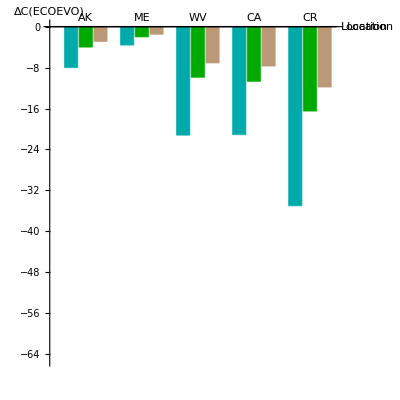

```mathematica
BarChart[{{-8,-4,-2.9},{-3.6,-2,-1.5},{-21.2,-9.9,-7.1},{-21.1,-10.7,-7.7},{-35,-16.5,-11.8}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"} ]
```

### Figure 4h - MGE T-dependence

```mathematica
γMx=γMref+m(x-xref);
φγMx=φx/.γM->γMx;
φγMT0=φγMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014/.x->x0;
SC3ecoγMx=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014;
SC3ecoevoγMx=SC3ecox/.φ->φx/.γM->γMx/.m->-0.014;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.17};
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-7.95763

-3.17771

-17.8918

-16.9246

-27.587

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.34};
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-1.94902

-1.25094

-6.50224

-7.40929

-13.5531

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,m->-0.014,IS->5 10^-3,c->1.5};
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]
NIntegrate[ΔSCecoevoγM/.dM->dMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]
```

-1.35045

-0.920725

-4.63062

-5.44451

-9.90564

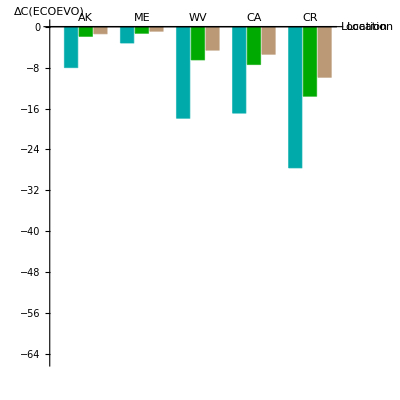

```mathematica
BarChart[{{-8,-1.9,-1.4},{-3.2,-1.3,-0.9},{-17.9,-6.5,-4.6},{-16.9,-7.4,-5.4},{-27.6,-13.6,-9.9}},
ChartLabels->{Placed[{"AK","ME","WV","CA","CR"},Above],None},
PlotRange->{Automatic,{-65,0}},
AxesOrigin->{0,0},
ChartStyle->{Darker[Cyan],Darker[Green],Lighter[Brown]},
BarSpacing->{0.1,1},
ImagePadding->{{30,40},{15,20}},AspectRatio->1,AxesLabel->{"Location","ΔC(ECOEVO)"} ]
```

## Does it change EVO to not take the integration? #AK: (1) 225, (2) 153 #ME: (1) 143, (2) 119 #WV: (1) 83, (2) 70 #CA: (1) 49, (2) 44 #CR: (1) 16, (2) 15

### (1) EVO = Integrate(EVOL) - Integrate(ECOS) / Integrate(ECOS)

```mathematica
100*(NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26, 31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26, 31}])/(NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26, 31}])
```

16.4354

### (2) EVO = EVOL - ECO / ECO

```mathematica
100*((ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR/.x->31) - (ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR/.x->31))/(ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR/.x->31)
```

14.5659

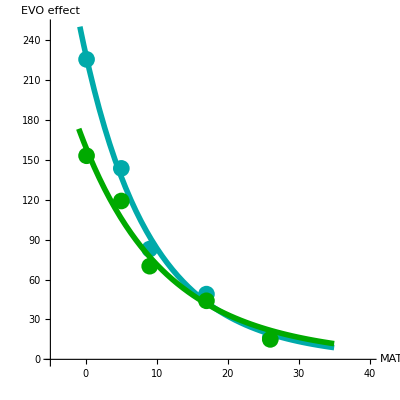

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,225.4},{5,143.5},{9,82.9},{17,49},{26,16.4}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{0,250}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,153},{5,119},{9,70},{17,44},{26,15}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2]
```

### Plot EVOL and ECOS = f(T)

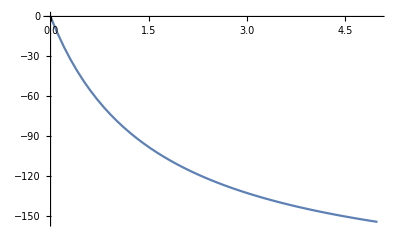

```mathematica
Plot[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0, 5}]
```

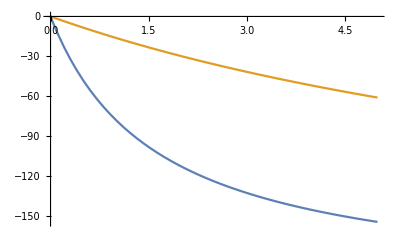

```mathematica
Plot[{ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK},{x,0, 5}]
```

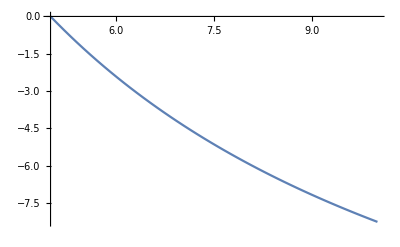

```mathematica
Plot[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5, 10}]
```

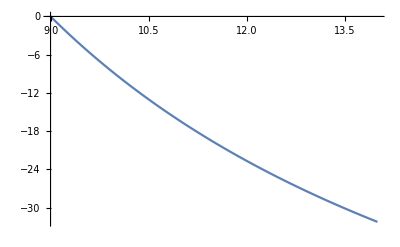

```mathematica
Plot[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9, 14}]
```

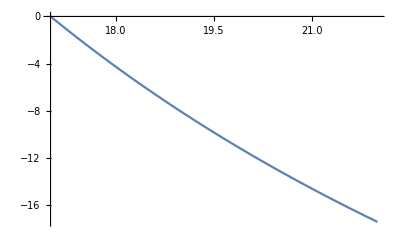

```mathematica
Plot[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17, 22}]
```

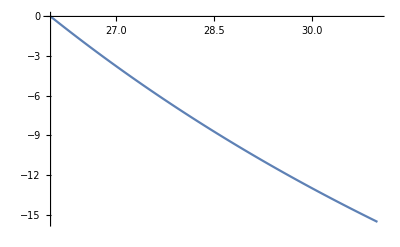

```mathematica
Plot[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26, 31}]
```

## Figure 4 (i-l) (ECOEVO) Note: we calculate the norm of the EVO effect (sign comes from comparing ECO and ECOEVO)

### Figure 4i - Baseline scenario

```mathematica
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.17};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

225.406

143.518

82.9245

49.0225

16.4354

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.34};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

123.255

57.9828

41.7093

25.2491

8.88161

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->0,IS->5 10^-3,c->1.5};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

84.565

40.2143

30.2986

18.5993

6.64983

```mathematica
dataEVO1={{0.1,225.4},{5,143.5},{9,82.9},{17,49},{26,16.4}};
dataEVO2={{0.1,123.3},{5,58},{9,41.7},{17,25.2},{26,8.9}};
dataEVO3={{0.1,84.6},{5,40.2},{9,30.3},{17,18.6},{26,6.6}};
```

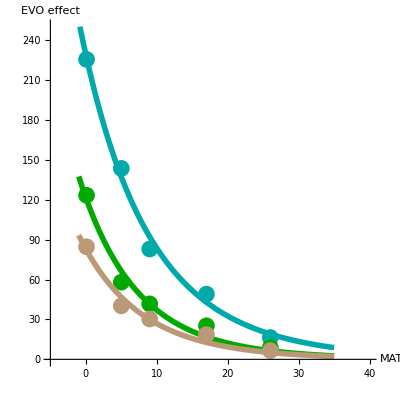

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,225.4},{5,143.5},{9,82.9},{17,49},{26,16.4}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{0,250}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,123.3},{5,58},{9,41.7},{17,25.2},{26,8.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,84.6},{5,40.2},{9,30.3},{17,18.6},{26,6.6}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

### Figure 4j - Low mortality T-dependence (EdM = 25)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.17};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

36.0401

23.1028

18.9924

16.5361

7.94549

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.34};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

18.4599

11.1387

9.96915

8.51048

4.14794

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->25,IS->5 10^-3,c->1.5};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

13.6204

8.09905

7.40261

6.28965

3.07578

```mathematica
dataEVO4={{0.1,36},{5,23.1},{9,19},{17,16.5},{26,7.9}};
dataEVO5={{0.1,18.5},{5,11.1},{9,10},{17,8.5},{26,4.1}};
dataEVO6={{0.1,13.6},{5,8.1},{9,7.4},{17,6.3},{26,3.1}};
```

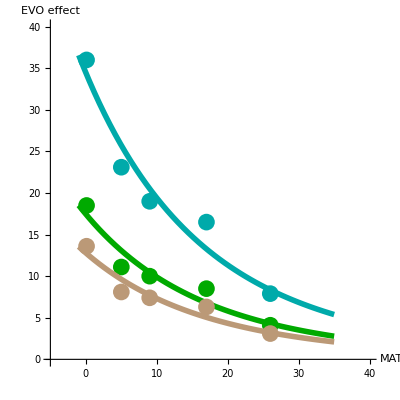

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,36},{5,23.1},{9,19},{17,16.5},{26,7.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{0,40}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,18.5},{5,11.1},{9,10},{17,8.5},{26,4.1}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,13.6},{5,8.1},{9,7.4},{17,6.3},{26,3.1}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

### Figure 4k - High mortality T-dependence (EdM = 55)

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.17};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

17.0247

14.2821

15.4156

21.2815

16.9172

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.34};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

9.63055

7.55109

8.44883

10.9349

8.22986

```mathematica
testγMdMIc0={dMref->2 10^-4,EadM->55,IS->5 10^-3,c->1.5};
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testAK,{x,0,5}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testME,{x,5,10}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testWV,{x,9,14}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCA,{x,17,22}]]*100
Abs[NIntegrate[ΔSCecoevodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]-NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]/Abs[NIntegrate[ΔSCecodM/.γM->γMref/.testpar/.testγMdMIc0/.testCR,{x,26,31}]]*100
```

7.35043

5.6451

6.38159

8.1098

5.99928

```mathematica
dataEVO7={{0.1,-17},{5,-14.3},{9,-15.4},{17,-21.3},{26,-16.9}};
dataEVO8={{0.1,-9.6},{5,-7.6},{9,-8.4},{17,-10.9},{26,-8.2}};
dataEVO9={{0.1,-7.4},{5,-5.6},{9,-6.4},{17,-8.1},{26,-6}};
```

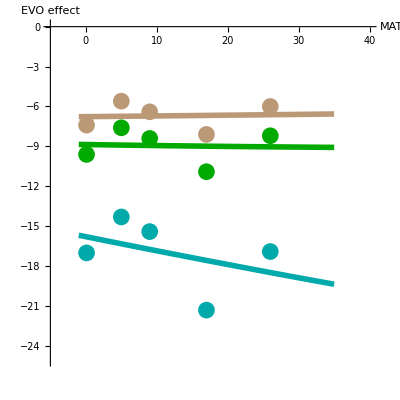

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,-17},{5,-14.3},{9,-15.4},{17,-21.3},{26,-16.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{-25,0}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,-9.6},{5,-7.6},{9,-8.4},{17,-10.9},{26,-8.2}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,-7.4},{5,-5.6},{9,-6.4},{17,-8.1},{26,-6}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

### Figure 4l - MGE T-dependence

```mathematica
γMx=γMref+m(x-xref);
φγMx=φx/.γM->γMx;
φγMT0=φγMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014/.x->x0;
SC3ecoγMx=SC3ecox/.φ->φγMT0/.γM->γMx/.m->-0.014;
SC3ecoevoγMx=SC3ecox/.φ->φx/.γM->γMx/.m->-0.014;
ΔSCecoγM=SC3ecoγMx-SC3adaptT0;
ΔSCecoevoγM=SC3ecoevoγMx-SC3adaptT0;
testpar={eC->10^-6,eD->10^-2,dZ->2 10^-3,VmU0->10^5,EvU->38,KmU0->1.6 10^3,EkU->21,R->8.314 10^-3,γZ->0.4,γMref->0.31,xref->20};
testAK={x0->0,VmD0->7.7 10^7,EvD->43.7,KmD0->2.79 10^7,EkD->26.2};
testME={x0->5,VmD0->7.73 10^9,EvD->50.6,KmD0->2.1 10^7,EkD->23.8};
testWV={x0->9,VmD0->1.35 10^8,EvD->47.2,KmD0->3.1 10^6,EkD->21.4};
testCA={x0->17,VmD0->1.15 10^6,EvD->36.1,KmD0->3.3 10^4,EkD->9.7};
testCR={x0->26,VmD0->1.23 10^8,EvD->48.9,KmD0->4.4 10^3,EkD->5.2};
```

```mathematica
dataEVO7={{0.1,990.6},{5,89.9},{9,54.2},{17,20.6},{26,-16.7}};
dataEVO8={{0.1,198.9},{5,34.8},{9,24.9},{17,9.6},{26,-8.2}};
dataEVO9={{0.1,89.8},{5,22},{9,16.6},{17,6.6},{26,-5.9}};
```

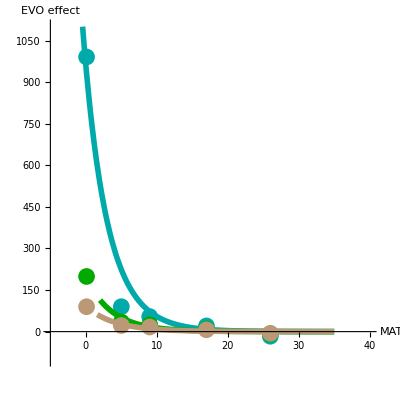

```mathematica
Off[NonlinearModelFit::cvmit]
dataEVO={{0.1,990.6},{5,89.9},{9,54.2},{17,20.6},{26,-16.7}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot1=Show[Plot[nlmEVO[x],{x,-1,35},PlotRange->{{-5,40},{-100,1100}},AxesOrigin->{-5,0},PlotStyle->{Darker[Cyan],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Cyan],PointSize[0.03]}],AspectRatio->1,AxesLabel->{"MAT","EVO effect"}];
dataEVO={{0.1,198.9},{5,34.8},{9,24.9},{17,9.6},{26,-8.2}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot2=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Darker[Green],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Darker[Green],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
dataEVO={{0.1,89.8},{5,22},{9,16.6},{17,6.6},{26,-5.9}};
nlmEVO=NonlinearModelFit[dataEVO,a/(8.314 10^-3(x+273)^c) Exp[b/(8.314 10^-3(x+273))],{a,b,c},x];
Plot3=Show[Plot[nlmEVO[x],{x,-1,35},AxesOrigin->{-5,0},PlotStyle->{Lighter[Brown],Thickness[0.01]}],ListPlot[dataEVO,PlotStyle->{Lighter[Brown],PointSize[0.03]}],LabelStyle->Directive[FontSize->20],ImageSize->400];
Show[Plot1,Plot2,Plot3]
```

## Supplementary Figure 2 (steady states=f(phi))

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-4,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dM->2 10^-4,γM->0.31,VmU0->7.3 10^5,EvU->35,x->20};
COND1φ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2φ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3φ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4φ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoφ=M3ecox/.testparam;
```

### Supplementary Figure 2a (M)

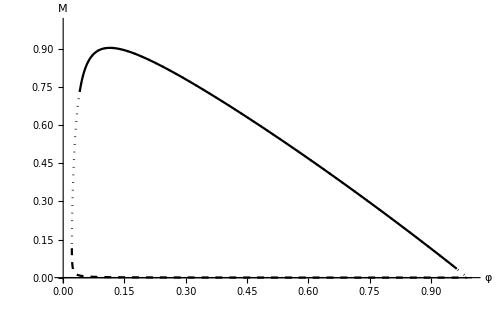

```mathematica
Plot1=Plot[{Meq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,1}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","M"}];
Plot2=Plot[{Meq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,M3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,1}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{M3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,1}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

### Supplementary Figure 2b (Z)

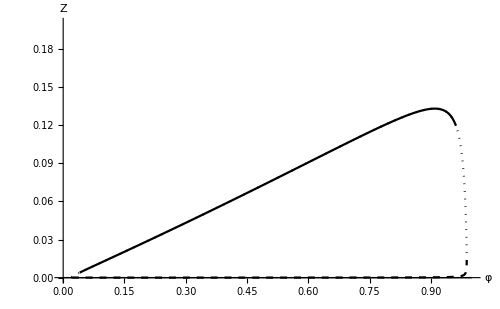

```mathematica
Plot1=Plot[{Zeq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.2}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","Z"}];
Plot2=Plot[{Zeq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,Z3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,0.2}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{Z3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.2}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

### Supplementary Figure 2c

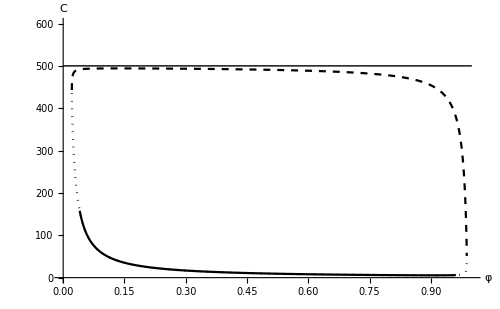

```mathematica
Plot1=Plot[{SCeq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,600}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","C"}];
Plot2=Plot[{SCeq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,SC3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,600}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{SC3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,600}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

### Supplementary Figure 2d (D)

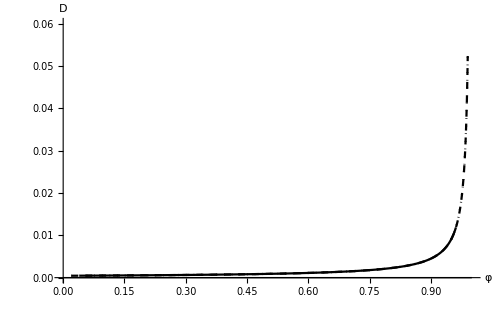

```mathematica
Plot1=Plot[{DCeq1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.06}},
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","D"}];
Plot2=Plot[{DCeq2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam,DC3ecox/.testparam},
{φ,0.02,0.99},PlotRange->{{0,1},{0,0.06}},
PlotStyle->{{Black,Dashed},{Black,Dotted}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Plot3=Plot[{DC3ecox/.testparam},
{φ,0,1},PlotRange->{{0,1},{0,0.06}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoφ]==0&&M3ecoφ>0&&COND1φ>0&&COND2φ>0&&COND3φ>0&&COND4φ>0]],
PlotStyle->{{Black}},LabelStyle->Directive[FontSize->20],ImageSize->500];
Show[Plot1,Plot3,Plot2]
```

## Supplementary Figure 3 (C=f(phi))

### Supplementary Figure 3a (γM)

### default

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,x->20};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
Plot0=Plot[SC3ecox/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,200}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black}}];
```

### min/max

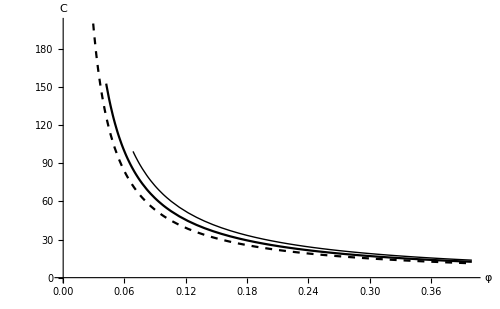

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.2,γZ->0.4,x->20};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotA=Plot[SC3ecox/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,200}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Thick}},ImageSize->500,AxesLabel->{"φ","C"}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.4,γZ->0.4,x->20};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotB=Plot[SC3ecox/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,200}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Dashed}}];
Show[PlotA,Plot0,PlotB]
```

## Supplementary Figure 4 (C=f(T))

### Supplementary Figure 4a (γM)

### default

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,φ->0.1};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
Plot0=Plot[SC3ecox/.testparam,{x,0,40},PlotRange->{{0,40},{0,200}},
RegionFunction->Function[{x,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black}}];
```

### min/max

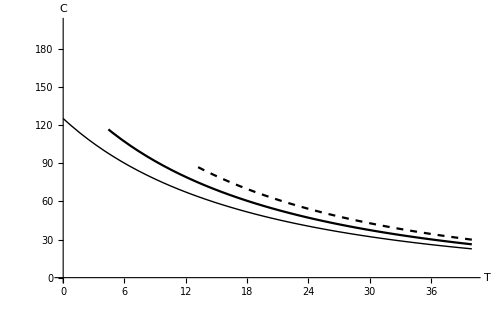

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.2,γZ->0.4,φ->0.1};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotA=Plot[SC3ecox/.testparam,{x,0,40},PlotRange->{{0,40},{0,200}},
RegionFunction->Function[{x,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Dashed}},ImageSize->500,AxesLabel->{"T","C"}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.4,γZ->0.4,φ->0.1};
COND1paramx=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND2paramx=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND3paramx=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
COND4paramx=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.testparam;
M3ecoparamx=M3ecox/.testparam;
PlotB=Plot[SC3ecox/.testparam,{x,0,40},PlotRange->{{0,40},{0,200}},
RegionFunction->Function[{x,z},Evaluate[Im[M3ecoparamx]==0&&M3ecoparamx>0&&COND1paramx>0&&COND2paramx>0&&COND3paramx>0&&COND4paramx>0]],
PlotStyle->{{Black,Thick}}];
Show[PlotA,Plot0,PlotB]
```

## Supplementary Figure 5 (phi=f(ΔT))

### Supplementary Figure 5a and Supplementary Figure 5e

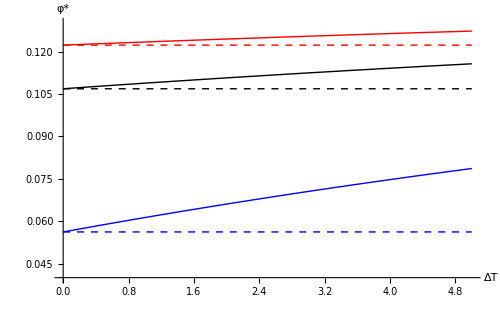

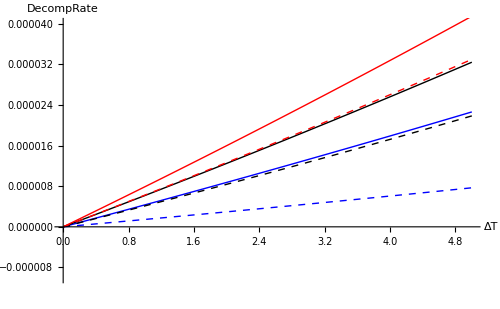

```mathematica
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->5,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
txdecompx=VmD Z/(KmD+SC)/.Z->Zeq3/.SC->SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+dx;
txdecompadaptT0=txdecompx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
txdecompecodMx=txdecompx/.φ->φdMT0/.dM->dMx/.testparam;
txdecompecoevodMx=txdecompx/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔecotxdecompdM=txdecompecodMx-txdecompadaptT0;
ΔecoevotxdecompdM=txdecompecoevodMx-txdecompadaptT0;
Plot1=Plot[{φdMT0/.testparam,φdMx/.testparam},{dx,0,5},AxesOrigin->{0,0.04},PlotRange->{{0,5},{0.04,0.13}},PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick}},ImageSize->500,AxesLabel->{"ΔT","φ*"}];
Plot2=Plot[{ΔecotxdecompdM,ΔecoevotxdecompdM},{dx,0,5},AxesOrigin->{0,0},PlotRange->{{0,5},{-10^-5,4 10^-5}},PlotStyle->{{Blue,Dashed,Thick},{Blue,Thick}},ImageSize->500,AxesLabel->{"ΔT","DecompRate"}];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->20,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
txdecompx=VmD Z/(KmD+SC)/.Z->Zeq3/.SC->SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+dx;
txdecompadaptT0=txdecompx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
txdecompecodMx=txdecompx/.φ->φdMT0/.dM->dMx/.testparam;
txdecompecoevodMx=txdecompx/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔecotxdecompdM=txdecompecodMx-txdecompadaptT0;
ΔecoevotxdecompdM=txdecompecoevodMx-txdecompadaptT0;
Plot3=Plot[{φdMT0/.testparam,φdMx/.testparam},{dx,0,5},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500];
Plot4=Plot[{ΔecotxdecompdM,ΔecoevotxdecompdM},{dx,0,5},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500];
testparam={eC->10^-6,eD->10^-2,dZ->2 10^-3,IS->5 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,dMref->2 10^-4,γM->0.31,VmU0->10^5,EvU->38,c->1.17,T0->30,xref->20,EadM->0};
dMx=dMref Exp[-EadM/R(1/((T0+dx)+273)-1/(xref+273))];
φdMx=φx/.x->T0+dx/.dM->dMx;
φdMT0=φdMx/.dx->0;
SC3adaptT0=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
SC3ecodMx=SC3ecox/.x->T0+dx/.φ->φdMT0/.dM->dMx/.testparam;
SC3ecoevodMx=SC3ecox/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
txdecompx=VmD Z/(KmD+SC)/.Z->Zeq3/.SC->SCeq3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+dx;
txdecompadaptT0=txdecompx/.φ->φdMT0/.dM->dMx/.dx->0/.testparam;
txdecompecodMx=txdecompx/.φ->φdMT0/.dM->dMx/.testparam;
txdecompecoevodMx=txdecompx/.φ->φx/.x->T0+dx/.dM->dMx/.testparam;
ΔecotxdecompdM=txdecompecodMx-txdecompadaptT0;
ΔecoevotxdecompdM=txdecompecoevodMx-txdecompadaptT0;
Plot5=Plot[{φdMT0/.testparam,φdMx/.testparam},{dx,0,5},PlotStyle->{{Red,Dashed,Thick},{Red,Thick}},ImageSize->500];
Plot6=Plot[{ΔecotxdecompdM,ΔecoevotxdecompdM},{dx,0,5},PlotStyle->{{Red,Dashed,Thick},{Red,Thick}},ImageSize->500];
Show[Plot1,Plot3,Plot5]
Show[Plot2,Plot4,Plot6]
```

## Supplementary Figure 6 (ΔC=f(T))

### Supplementary Figure 6a1

53.2635

22.2288

12.4011

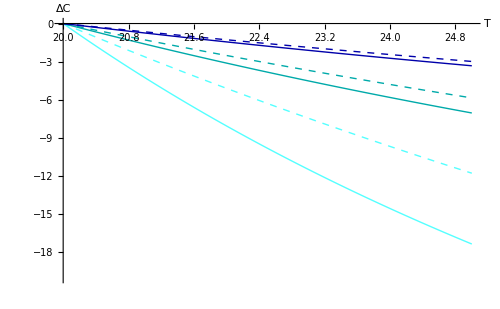

```mathematica
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.25,γZ->0.4,c->1.17,x0->20};
Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.testparam,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]*100
Plot1=Plot[{ΔSCeco/.testparam/.x0->20,ΔSCecoevo/.testparam/.x0->20},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-20,0}},PlotStyle->{{Lighter[Cyan],Dashed,Thick},{Lighter[Cyan],Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.5,γZ->0.4,c->1.17,x0->20};
Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.testparam,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]*100
Plot2=Plot[{ΔSCeco/.testparam/.x0->20,ΔSCecoevo/.testparam/.x0->20},{x,20,25},PlotStyle->{{Darker[Cyan],Dashed,Thick},{Darker[Cyan],Thick}}];
testparam={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.75,γZ->0.4,c->1.17,x0->20};
Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.testparam,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.testparam,{dx,0,5}]]*100
Plot3=Plot[{ΔSCeco/.testparam/.x0->20,ΔSCecoevo/.testparam/.x0->20},{x,20,25},PlotStyle->{{Darker[Blue],Dashed,Thick},{Darker[Blue],Thick}}];
Show[Plot1,Plot2,Plot3]
```

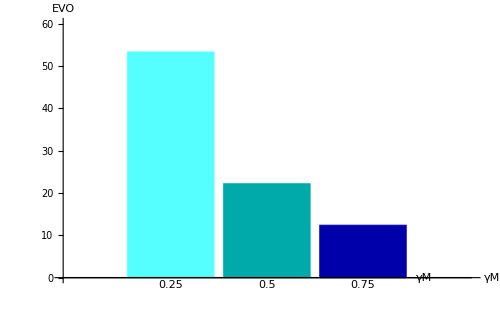

```mathematica
BarChart[{{53.3,22.2,12.4}},
ChartLabels->{"0.25","0.5","0.75"},
AxesLabel->{"γM","EVO"},
PlotRange->{Automatic,{0,60}},
ChartStyle->{Lighter[Cyan],Darker[Cyan],Darker[Blue]},
ImagePadding->{{20,40},{15,20}},ImageSize->500 ]
```

### Supplementary Figure 6a2

```mathematica
testxone={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM0->0.3,γZ->0.4,c->1.17,x0->20};
LPx=0.25;
HPx=0.75;
LOx=ΔSCeco/.x->x0+dx/.dx->5/.testxone/.γM->LPx;
HOx=ΔSCeco/.x->x0+dx/.dx->5/.testxone/.γM->HPx;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.24923

```mathematica
LOx=ΔSCecoevo/.x->x0+dx/.dx->5/.testxone/.γM->LPx;
HOx=ΔSCecoevo/.x->x0+dx/.dx->5/.testxone/.γM->HPx;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.50386

```mathematica
LOx=Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.γM->LPx/.testxone,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.γM->LPx/.testxone,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.γM->LPx/.testxone,{dx,0,5}]]*100;
HOx=Abs[NIntegrate[ΔSCecoevo/.x->x0+dx/.γM->HPx/.testxone,{dx,0,5}]-NIntegrate[ΔSCeco/.x->x0+dx/.γM->HPx/.testxone,{dx,0,5}]]/Abs[NIntegrate[ΔSCeco/.x->x0+dx/.γM->HPx/.testxone,{dx,0,5}]]*100;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.32664

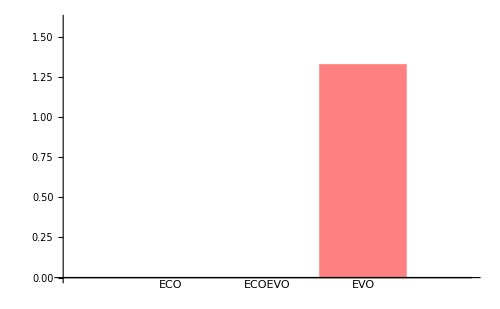

```mathematica
BarChart[{{1.249232907351444,1.5038615204491705,1.3266426887693321}},
ChartLabels->{"ECO","ECOEVO","EVO"},
PlotRange->{Automatic,{0,1.6}},
ChartStyle->{Directive[EdgeForm[{Thickness[0.005],AbsoluteDashing[{5,15-5}]}],White],Directive[EdgeForm[Thickness[0.005]],White],Pink},
ImagePadding->{{20,40},{15,20}},ImageSize->500 ]
```

## Supplementary Figure 7 (ΔC=f(EvD,v0D))

### Supplementary Figure 7a

```mathematica
testv0DEvD={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD00->1.15 10^6,EvD0->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20};
COND1γZdZ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
COND2γZdZ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
COND3γZdZ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
COND4γZdZ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testv0DEvD;
M3ecoγZdZ=M3ecox/.φ->φx/.x->x0/.testv0DEvD;
```

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testv0DEvD,{x,20,25}]-NIntegrate[ΔSCeco/.testv0DEvD,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testv0DEvD,{x,20,25}]],
{VmD0,5 10^5,5 10^7},{EvD,30,50},
RegionFunction->Function[{VmD0,EvD,z},Evaluate[Im[M3ecoγZdZ]==0&&M3ecoγZdZ>0&&COND1γZdZ>0&&COND2γZdZ>0&&COND3γZdZ>0&&COND4γZdZ>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"EvD",},{"v0D",}},LabelStyle->Directive[FontSize->20]]
```

-Graphics-

### Supplementary Figure 7b

```mathematica
testK0DEKD={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD00->3.3 10^4,EkD0->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20};
COND1γZdZ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
COND2γZdZ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
COND3γZdZ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
COND4γZdZ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testK0DEKD;
M3ecoγZdZ=M3ecox/.φ->φx/.x->x0/.testK0DEKD;
```

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testK0DEKD,{x,20,25}]-NIntegrate[ΔSCeco/.testK0DEKD,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testK0DEKD,{x,20,25}]],
{KmD0,5 10^3,5 10^4},{EkD,5,25},
RegionFunction->Function[{KmD0,EkD,z},Evaluate[Im[M3ecoγZdZ]==0&&M3ecoγZdZ>0&&COND1γZdZ>0&&COND2γZdZ>0&&COND3γZdZ>0&&COND4γZdZ>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"EkD",},{"K0D",}},LabelStyle->Directive[FontSize->20]]
```

-Graphics-

### Supplementary Figure 7c

```mathematica
testγZdZ={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ0->2 10^-3,IS->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ0->0.4,c->1.1131,x0->20};
COND1γZdZ=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
COND2γZdZ=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
COND3γZdZ=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
COND4γZdZ=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testγZdZ;
M3ecoγZdZ=M3ecox/.φ->φx/.x->x0/.testγZdZ;
```

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testγZdZ,{x,20,25}]-NIntegrate[ΔSCeco/.testγZdZ,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testγZdZ,{x,20,25}]],
{γZ,0,1},{dZ,5 10^-4,5 10^-3},
RegionFunction->Function[{γZ,dZ,z},Evaluate[Im[M3ecoγZdZ]==0&&M3ecoγZdZ>0&&COND1γZdZ>0&&COND2γZdZ>0&&COND3γZdZ>0&&COND4γZdZ>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"dZ",},{"γZ",}},LabelStyle->Directive[FontSize->20]]
```

-Graphics-

### Supplementary Figure 7d

```mathematica
testISeD={eC->10^-6,eD0->10^-2,dM->2 10^-4,dZ->2 10^-3,IS0->5 10^-3,VmU0->10^5,EvU->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20};
COND1ISeD=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
COND2ISeD=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
COND3ISeD=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
COND4ISeD=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.x->x0/.testISeD;
M3ecoISeD=M3ecox/.φ->φx/.x->x0/.testISeD;
```

```mathematica
ContourPlot[Abs[NIntegrate[ΔSCecoevo/.testISeD,{x,20,25}]-NIntegrate[ΔSCeco/.testISeD,{x,20,25}]]/Abs[NIntegrate[ΔSCeco/.testISeD,{x,20,25}]],
{eD,10^-3,10^-2},{IS,10^-3,10^-2},
RegionFunction->Function[{eD,IS,z},Evaluate[Im[M3ecoISeD]==0&&M3ecoISeD>0&&COND1ISeD>0&&COND2ISeD>0&&COND3ISeD>0&&COND4ISeD>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"I",},{"eD",}},LabelStyle->Directive[FontSize->20]]
```

-Graphics-

## Supplementary Figure 8 (ΔC=f(dM,γM))

### Supplementary Figure 8a

```mathematica
Off[Power::infy]
Off[Infinity::indet]
testgmdm={eC->10^-6,eD->10^-2,dM0->2 10^-4,EadM->25,dZ->2 10^-3,IS->5 10^-3,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM0->0.31,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testgmdm;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testgmdm;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testgmdm;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1gmdm=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND2gmdm=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND3gmdm=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
COND4gmdm=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
M3ecogmdm=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testgmdm;
Plot2=ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{γM,0,0.3},{dMref,2 10^-4,2 10^-3},
RegionFunction->Function[{γM,dMref,z},Evaluate[Im[M3ecogmdm]==0&&M3ecogmdm>0&&COND1gmdm>0&&COND2gmdm>0&&COND3gmdm>0&&COND4gmdm>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"dMref",},{"γM",}},LabelStyle->Directive[FontSize->20]]
```

-Graphics-

### Supplementary Figure 8b

```mathematica
testEvUV0U={eC->10^-6,eD->10^-2,dMref->2 10^-4,EadM->25,dZ->2 10^-3,IS->5 10^-3,VmU00->10^5,EvU0->38,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,c->1.1131,x0->20,xref->20};
dMx=dMref Exp[-EadM/R(1/(x+273)-1/(xref+273))];
φdMx=φx/.dM->dMx;
φdMT0=φdMx/.x->x0;
SC3adaptT0=SC3ecox/.φ->φdMT0/.dM->dMx/.x->x0/.testEvUV0U;
SC3ecodMx=SC3ecox/.φ->φdMT0/.dM->dMx/.testEvUV0U;
SC3ecoevodMx=SC3ecox/.φ->φx/.dM->dMx/.testEvUV0U;
ΔSCecodM=SC3ecodMx-SC3adaptT0;
ΔSCecoevodM=SC3ecoevodMx-SC3adaptT0;
COND1EvV0U=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND2EvV0U=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND3EvV0U=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
COND4EvV0U=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
M3ecoEvV0U=M3ecox/.φ->φx/.dM->dMx/.x->x0/.testEvUV0U;
ContourPlot[Abs[NIntegrate[ΔSCecoevodM,{x,20,25}]-NIntegrate[ΔSCecodM,{x,20,25}]]/Abs[NIntegrate[ΔSCecodM,{x,20,25}]],
{EvU,30,50},{VmU0,10^5,2 10^6},
RegionFunction->Function[{EvU,VmU0,z},Evaluate[Im[M3ecoEvV0U]==0&&M3ecoEvV0U>0&&COND1EvV0U>0&&COND2EvV0U>0&&COND3EvV0U>0&&COND4EvV0U>0]],
PlotRange->Full,ColorFunction->ColorData[{"ValentineTones",{1,0}}],ColorFunctionScaling->False,Contours->{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9},ContourLabels->True,FrameLabel->{{"v0U",},{"EvU",}},LabelStyle->Directive[FontSize->20]]
```

-Graphics-

## Supplementary Figure 9 (C=f(phi))

### Supplementary Figure 9a

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,T0->20};
COND1paramT0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND2paramT0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND3paramT0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND4paramT0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
M3ecoparamT0=M3ecox/.x->T0/.testparam;
COND1paramT1=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
COND2paramT1=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
COND3paramT1=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
COND4paramT1=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0+5/.testparam;
M3ecoparamT1=M3ecox/.x->T0+5/.testparam;
Plot2a=Plot[SC3ecox+M3ecox+Z3ecox+DC3ecox/.x->T0+5/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,6000}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT1]==0&&M3ecoparamT1>0&&COND1paramT1>0&&COND2paramT1>0&&COND3paramT1>0&&COND4paramT1>0]],
PlotStyle->{Black,Thick},LabelStyle->Directive[FontSize->20],ImageSize->700];
Plot2b=Plot[SC3ecox+M3ecox+Z3ecox+DC3ecox/.x->T0/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,6000}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT0]==0&&M3ecoparamT0>0&&COND1paramT0>0&&COND2paramT0>0&&COND3paramT0>0&&COND4paramT0>0]],
PlotStyle->{Black}];
Plot2c=Plot[SCeq1/.testparam,{φ,0,0.4},PlotRange->{{0,0.4},{0,6000}},PlotStyle->{Black,Dashed,Thick}];
Show[Plot2a,Plot2b,Plot2c]
```

-Graphics-

### Supplementary Figure 9b

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,T0->20};
COND1paramT0=COND1/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND2paramT0=COND2/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND3paramT0=COND3/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
COND4paramT0=COND4/.VmD->VmDx/.KmD->KmDx/.VmU->VmUx/.KmU->KmUx/.x->T0/.testparam;
M3ecoparamT0=M3ecox/.x->T0/.testparam;
Plot1=Plot[{M3ecox/.x->T0/.testparam,Z3ecox/.x->T0/.testparam,SC3ecox/.x->T0/.testparam,DC3ecox/.x->T0/.testparam},{φ,0,1},PlotRange->{{0,0.4},{0,6000}},
RegionFunction->Function[{φ,z},Evaluate[Im[M3ecoparamT0]==0&&M3ecoparamT0>0&&COND1paramT0>0&&COND2paramT0>0&&COND3paramT0>0&&COND4paramT0>0]],
PlotStyle->{{Blue,Thick},{Magenta,Thick},{Green,Thick},{Orange,Thick}},LabelStyle->Directive[FontSize->20],ImageSize->700]
```

-Graphics-

## Supplementary Figure 10 (ΔC=f(T))

### Supplementary Figure 10a

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,x0->20,c->1.075};
Plot[{ΔCtoteco/.testparam,ΔCtotecoevo/.testparam},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-1000,2000}},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}]
```

-Graphics-

### Supplementary Figure 10b

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,x0->20,c->1.12};
Plot[{ΔCtoteco/.testparam,ΔCtotecoevo/.testparam},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-100,200}},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}]
```

-Graphics-

### Supplementary Figure 10c

```mathematica
testparam={IS->3 10^-3,VmU0->4 10^3,EvU->46,dM->10^-6,eC->5 10^-6,γM->0.7,eD->10^-2,dZ->2 10^-3,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γZ->0.4,x0->20,c->1.35};
Plot[{ΔCtoteco/.testparam,ΔCtotecoevo/.testparam},{x,20,25},AxesOrigin->{20,0},PlotRange->{{20,25},{-100,200}},PlotStyle->{{Black,Dashed,Thick},{Black,Thick}},ImageSize->500,AxesLabel->{"T","ΔC"}]
```

-Graphics-

## Supplementary Table 1 (Arrhenius parameter values)

### VmD

### 1) Calculate aVD CA, β-Glucosidase: Vint = 4.93, Vslope = 0.046 and if I want Allison’s 20°C-value (0.42) --> I need aVD = 1.2x10-3

```mathematica
Solve[aV Exp[Vint+Vslope x]==0.42,aV]/.x->20/.Vint->4.93/.Vslope->0.046
```

{{aV→0.00120956}}

### 2) Calculate VmD at several T to build a dataset

```mathematica
1.2 10^-3Exp[Vint+Vslope x]/.Vint->4.93/.Vslope->0.046/.x->10
```

0.263044

### 3) Fit the dataset with an Arrhenius to find V0D and EvD --> V0D = 1.15 x 10^6, EvD = 36.1

```mathematica
dataVmD={{0,0.16605541480795272},{10,0.26304406266474534},{20,0.4166812565744813},{30,0.6600539385744466},{40,1.0455742727889266},{50,1.6562670049044623}};
```

```mathematica
nlmVmD=NonlinearModelFit[dataVmD,VmD0 Exp[-EvD/(R(x+273))]/.R->8.314 10^-3,{VmD0,EvD},x]
Normal[nlmVmD]
Show[Plot[nlmVmD[x],{x,0,50},PlotRange->{{0,50},{0,2}}],ListPlot[dataVmD,PlotStyle->{Red,PointSize[0.02]}],Frame->True]
nlmVmD["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

FittedModel[1.14842×10^6 ⅇ^(-4347.06/(273+x))]

1.14842×10^6 ⅇ^(-4347.06/(273+x))

-Graphics-

0.000330084

```mathematica
Solve[4347.058585613794==EvD/R,EvD]/.R->8.314 10^-3
```

{{EvD→36.1414}}

#### 4) Plot

```mathematica
Plot[{1.2 10^-3Exp[Vint+Vslope x]/.Vint->4.93/.Vslope->0.046,1.15 10^6 Exp[-36.1/(R(x+273))]/.R->8.314 10^-3},{x,0,50},PlotRange->{{0,50},{0,2}},AxesLabel->{"T","VmD"},PlotStyle->{Orange,Cyan},PlotLegends->{"German 2012","Arrhénius"},ImageSize->500]
```

-Graphics-

## Supplementary Table 2 (Sensitivity analysis)

### Temperature (x)

```mathematica
testxone={eC->10^-6,eD->10^-2,dM->2 10^-4,dZ->2 10^-3,IS->5 10^-4,VmU0->7.3 10^5,EvU->35,VmD0->1.15 10^6,EvD->36.1,KmU0->1.6 10^3,EkU->21,KmD0->3.3 10^4,EkD->9.7,R->8.314 10^-3,γM->0.3,γZ->0.4,φ->0.1,x0->20};
LPx=4.9;
HPx=490;
LOx=SC3ecox/.x->LPx/.testxone;
HOx=SC3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

1.62621

```mathematica
LOx=DC3ecox/.x->LPx/.testxone;
HOx=DC3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

0.837385

```mathematica
LOx=M3ecox/.x->LPx/.testxone;
HOx=M3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

0.0598614

```mathematica
LOx=Z3ecox/.x->LPx/.testxone;
HOx=Z3ecox/.x->HPx/.testxone;
SA/.HO->HOx/.LO->LOx/.HP->HPx/.LP->LPx
```

0.0598614

## Supplementary Table 3 (5 biomes Arrhenius parameter values)

### VmD (Costa Rica) --> EvD = 48.9, V0D = 1.23 x 10^8

```mathematica
aV Exp[Vint+Vslope x]/.aV->1.2 10^-3/.Vint->4.11/.Vslope->0.061/.x->0
```

0.0731361

```mathematica
dataVmD={{0,0.07313606108354667},{10,0.1346019032013711},{20,0.2477255689875699},{30,0.45592191544577043},{40,0.8390930085790629},{50,1.5442931194870564}};
```

```mathematica
nlmVmD=NonlinearModelFit[dataVmD,VmD0 Exp[-EvD/(R(x+273))]/.R->8.314 10^-3,{VmD0,EvD},x]
Normal[nlmVmD]
Show[Plot[nlmVmD[x],{x,0,50},PlotRange->{{0,50},{0,2}}],ListPlot[dataVmD,PlotStyle->{Red,PointSize[0.02]}],Frame->True]
nlmVmD["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

FittedModel[1.23174×10^8 ⅇ^(-5878.73/(273+x))]

1.23174×10^8 ⅇ^(-5878.73/(273+x))

-Graphics-

0.000202851

```mathematica
Solve[5878.734148905386==EvD/R,EvD]/.R->8.314 10^-3
```

{{EvD→48.8758}}

### KmD (Costa Rica) --> EkD = 5.2, K0D = 5.5 x 10^3

```mathematica
aK Exp[Kint+Kslope x]/.aK->16.56/.Kint->3.32/.Kslope->0.007/.x->50
```

650.012

```mathematica
dataKmD={{0,458.0554052490373},{10,491.268169597308},{20,526.8891310828969},{30,565.092903700332},{40,606.0667623873072},{50,650.0115610466424}};
```

```mathematica
nlmKmD=NonlinearModelFit[dataKmD,KmD0 Exp[-EkD/(R(x+273))]/.R->8.314 10^-3,{KmD0,EkD},x]
Normal[nlmKmD]
Show[Plot[nlmKmD[x],{x,0,50},PlotRange->{{0,50},{0,700}}],ListPlot[dataKmD,PlotStyle->{Red,PointSize[0.02]}],Frame->True]
nlmKmD["EstimatedVariance",VarianceEstimatorFunction->(Mean[#^2]&)]
```

FittedModel[4442.78 ⅇ^(-622.9/(273+x))]

4442.78 ⅇ^(-622.9/(273+x))

-Graphics-

10.2315

```mathematica
Solve[622.9003784602833==EkD/R,EkD]/.R->8.314 10^-3
```

{{EkD→5.17879}}